## τα from fitting CRSISF, SISF to stretched exponential

```mathematica
(*saveFolder="/Users/chengling/Learning/Research/TempDirForRemote/p380TauAlpha/N4096/";*)
```

```mathematica
saveFolder="/home/chengling/Research/Project/Cell/glassyDynamics/N4096/";
```

```mathematica
Directory[]
```

/home/chengling

## p0=3.80, N= 4096

```mathematica
stretchedExp[t_,G_,τ_,β_]:=G Exp[-(t/τ)^β];
```

```mathematica
Tlist={0.08868,0.05586,0.05409,0.03756, 0.03105 ,0.02652,0.01945,0.01782,0.01471,0.01141, 0.01023 ,0.005873, 0.003371};
```

```mathematica
Tstring=ToString[NumberForm[#,{9,8},ExponentFunction->(Null&)]]&/@Tlist
```

{0.08868000,0.05586000,0.05409000,0.03756000,0.03105000,0.02652000,0.01945000,0.01782000,0.01471000,0.01141000,0.01023000,0.00587300,0.00337100}

```mathematica
wtlist={0.0,0.1,0.31,1.,3.16,10.,31.62,100.,316.22,1000.,3162.27}
```

{0.,0.1,0.31,1.,3.16,10.,31.62,100.,316.22,1000.,3162.27}

```mathematica
wtliststring=ToString[NumberForm[#,{9,6},ExponentFunction->(Null&)]]&/@wtlist
```

{0.000000,0.100000,0.310000,1.000000,3.160000,10.000000,31.620000,100.000000,316.220000,1000.000000,3162.270000}

```mathematica
test=Import["/Users/chengling/Learning/Research/TempDirForRemote/p380TauAlpha/N4096/ove","Data"]
```

<|/BoxMatrix→NumericArray[…],/additionalData→NumericArray[<90,8192>, Real64],/postion→NumericArray[<90,8192>, Real64],/time→NumericArray[…],/type→NumericArray[<90,4096>, Integer32],/velocity→NumericArray[<90,8192>, Real64]|>

### Test if waiting time actually works

```mathematica
timeWT=Table[Table[testdata=Import[StringJoin[saveFolder,"glassyDynamics_N4096_p3.8000_T",Tstring[[i]],"_waitingTime",wtliststring[[wt]],"_idx0.nc"],"Data"];Table[testdata[[4,j,1]]-testdata[[4,1,1]],{j,Length[testdata[[4]]]}],{wt,Length[wtlist]}],{i,Length[Tstring]}];
```

```mathematica
overlapCRSSIFWT=Table[Table[Import[StringJoin[saveFolder,"overlapCRSISF_N4096_p3.8000_T",Tstring[[T]],"_waitingTime",wtliststring[[wt]],"_idx0.nc"],"Data"],{wt,Length[wtlist]}],{T,Length[Tlist]}];
```

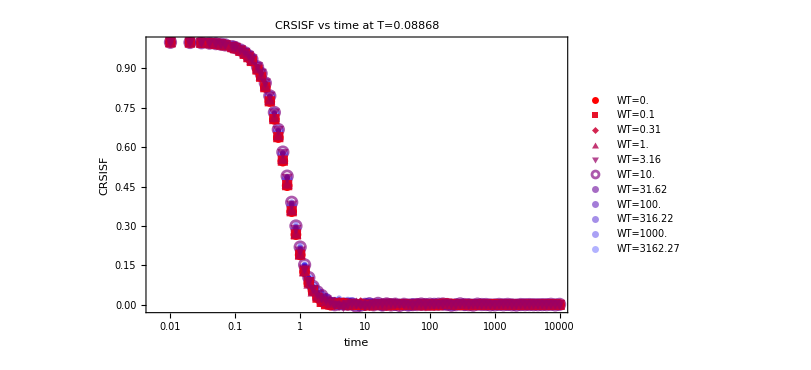

```mathematica
ListLogLinearPlot[Table[Table[{timeWT[[1,wt,rec]],Normal[overlapCRSSIFWT[[1,wt,2]]][[rec]]},{rec,Length[timeWT[[1,wt]]]}],{wt,1,11}],PlotLegends->Table["WT="<>ToString[wtlist[[wt]]],{wt,1,11}],PlotStyle->redBluePlotConfig[11],FrameLabel->{"time","CRSISF"},ImageSize->600,PlotLabel->"CRSISF vs time at T="<>ToString[Tlist[[1]]],PlotMarkers->Automatic]
```

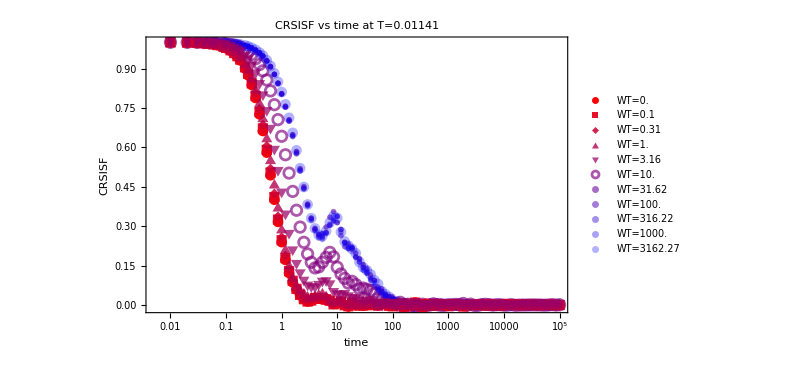

```mathematica
ListLogLinearPlot[Table[Table[{timeWT[[7,wt,rec]],Normal[overlapCRSSIFWT[[7,wt,2]]][[rec]]},{rec,Length[timeWT[[7,wt]]]}],{wt,1,11}],PlotLegends->Table["WT="<>ToString[wtlist[[wt]]],{wt,1,11}],PlotStyle->redBluePlotConfig[11],FrameLabel->{"time","CRSISF"},ImageSize->600,PlotLabel->"CRSISF vs time at T="<>ToString[Tlist[[7]]],PlotMarkers->Automatic]
```

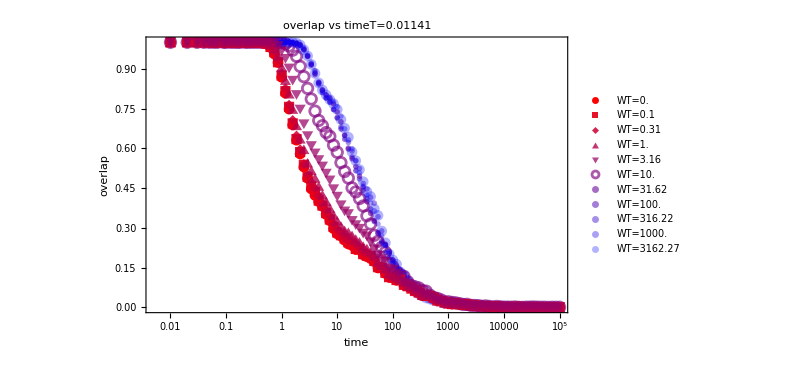

```mathematica
ListLogLinearPlot[Table[Table[{timeWT[[7,wt,rec]],Normal[overlapCRSSIFWT[[7,wt,1]]][[rec]]},{rec,Length[timeWT[[7,wt]]]}],{wt,1,11}],PlotLegends->Table["WT="<>ToString[wtlist[[wt]]],{wt,1,11}],PlotStyle->redBluePlotConfig[11],FrameLabel->{"time","overlap"},ImageSize->600,PlotLabel->"overlap vs timeT="<>ToString[Tlist[[7]]],PlotMarkers->Automatic]
```

### τα

```mathematica
longestWT={1000.,1000.,1000.,1000.,1000.,1000.,1000.,1000.,1000.,1000.,1000.,3162.27,10000.,10000.}
```

{1000.,1000.,1000.,1000.,1000.,1000.,1000.,1000.,1000.,1000.,1000.,3162.27,10000.,10000.}

```mathematica
longestWTstring=ToString[NumberForm[#,{9,6},ExponentFunction->(Null&)]]&/@longestWT
```

{1000.000000,1000.000000,1000.000000,1000.000000,1000.000000,1000.000000,1000.000000,1000.000000,1000.000000,1000.000000,1000.000000,3162.270000,10000.000000,10000.000000}

```mathematica
TauE={10.,10.,21.54 ,46.41, 21.54,100., 215.44,464.15,1000.,46.41 ,100., 215.44 ,464.15};
TauEString=ToString[NumberForm[#,{9,2},ExponentFunction->(Null&)]]&/@TauE
```

{10.00,10.00,21.54,46.41,21.54,100.00,215.44,464.15,1000.00,46.41,100.00,215.44,464.15}

```mathematica
{"1000.000000","10000.000000","10000.000000","10000.000000","10000.000000","10000.000000","10000.000000"}
```

```mathematica
overlap=Table[Table[Import[StringJoin[saveFolder,"overlap_N4096_p3.8000_T",Tstring[[T]],"_waitingTime",longestWTstring[[T]],"_idx",ToString[i],".nc"],"Data"],{i,2}],{T,Length[Tlist]}];
```

```mathematica
orientation=Table[Table[Import[StringJoin[saveFolder,"orientationalCorrelation_N4096_p3.8000_T",Tstring[[T]],"_waitingTime",longestWTstring[[T]],"_idx",ToString[i],".nc"],"Data"],{i,2}],{T,Length[Tlist]}];
```

```mathematica
SAC=Table[Table[Import[StringJoin[saveFolder,"SACtime_N4096_p3.8000_T",Tstring[[T]],"_waitingTime5times",TauEString[[T]],"_idx",ToString[i],".nc"],"Data"],{i,2}],{T,Length[Tlist]}];
```

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/SACtime_N4096_p3.8000_T0.08868000_waitingTime5times10.00_idx1.nc not found during Import.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/SACtime_N4096_p3.8000_T0.08868000_waitingTime5times10.00_idx2.nc not found during Import.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/SACtime_N4096_p3.8000_T0.05586000_waitingTime5times10.00_idx1.nc not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

```mathematica
SISF=Table[Table[Import[StringJoin[saveFolder,"SISF_N4096_p3.8000_T",Tstring[[T]],"_waitingTime",longestWTstring[[T]],"_idx",ToString[i],".nc"],"Data"],{i,2}],{T,Length[Tlist]}];
```

```mathematica
time=Table[testdata=Import[StringJoin[saveFolder,"glassyDynamics_N4096_p3.8000_T",Tstring[[T]],"_waitingTime",longestWTstring[[T]],"_idx1.nc"],"Data"];Table[testdata[[4,j,1]]-testdata[[4,1,1]],{j,Length[testdata[[4]]]}],{T,Length[Tstring]}];
```

```mathematica
overlapMean=Table[Table[Mean[Table[Normal[overlap[[T,i,1,rec]]],{i,2}]],{rec,Length[overlap[[T,1,1]]]}],{T,Length[Tlist]}];
```

```mathematica
overlapCRMean=Table[Table[Mean[Table[Normal[overlap[[T,i,2,rec]]],{i,2}]],{rec,Length[overlap[[T,1,1]]]}],{T,Length[Tlist]}];
```

```mathematica
SISFMean=Table[Table[Mean[Table[Normal[SISF[[T,i,1,rec]]],{i,2}]],{rec,Length[overlap[[T,1,1]]]}],{T,Length[Tlist]}];
```

```mathematica
SISFCRMean=Table[Table[Mean[Table[Normal[SISF[[T,i,2,rec]]],{i,2}]],{rec,Length[overlap[[T,1,1]]]}],{T,Length[Tlist]}];
```

```mathematica
orientationMeanReal=Table[Table[Mean[Table[Normal[orientation[[T,i,1,rec]]/orientation[[T,i,1,1]]],{i,2}]],{rec,Length[orientation[[T,1,1]]]}],{T,Length[Tlist]}];
```

```mathematica
orientationMeanIm=Table[Table[Mean[Table[Normal[orientation[[T,i,2,rec]]],{i,2}]],{rec,Length[orientation[[T,1,1]]]}],{T,Length[Tlist]}];
```

```mathematica
orientationMeanReal[[1]]
```

{1.,0.998812,0.996585,0.994656,0.991298,0.987666,0.983263,0.978189,0.966965,0.960296,0.945154,0.92935,0.911953,0.892719,0.851403,0.817164,0.769041,0.707413,0.63451,0.564599,0.477086,0.385759,0.294076,0.21448,0.145298,0.0911211,0.0578127,0.0370651,0.0285179,0.0239496,0.0192011,0.0114019,0.0114038,0.00404916,0.00596198,-0.0229211,-0.0142273,-0.00421327,0.0013686,0.00329229,-0.0106676,-0.0138074,0.000490274,-0.00263196,0.00167545,0.00205459,-0.0056839,0.00894408,-0.00100814,0.00295512,0.00116993,0.0141282,-0.000700802,0.00361619,-0.0000400757,0.0119886,-0.00513205,-0.00487675,0.00416165,0.00691193,0.0000561674,-0.00835322,0.00401818,-0.000584634,-0.00038398,-0.018035,0.00278123,-0.00236823,0.00251752,0.0104702,0.00481681,-0.00138902,0.0100714,0.00142255,0.000777859,-0.000749133,-0.000620157,0.00335959,0.0049324,-0.0121153,-0.00880683,0.0128544,-0.00112937,0.00753786}

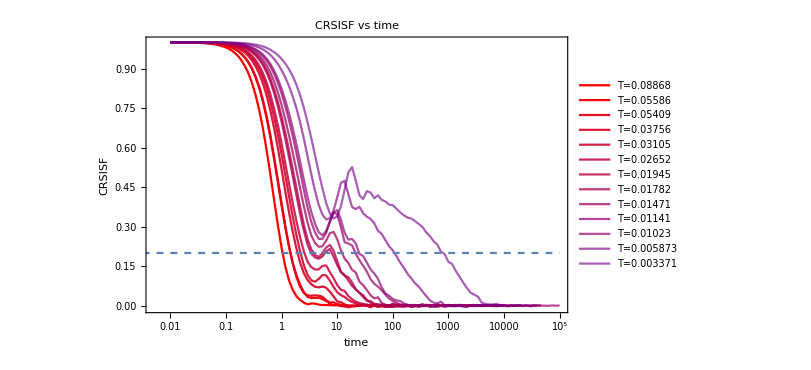

```mathematica
CRSISFPlot=ListLogLinearPlot[Table[Table[{time[[T,rec]],SISFCRMean[[T,rec]]},{rec,Length[SISFCRMean[[T]]]}],{T,Length[Tlist]}],PlotLegends->Table["T="<>ToString[Tlist[[T]]],{T,Length[Tlist]}],PlotStyle->redBluePlotConfig[Length[TlistAllT]],FrameLabel->{"time","CRSISF"},ImageSize->600,PlotLabel->"CRSISF vs time",Joined->True];
Show[CRSISFPlot,LogLinearPlot[0.2,{x,0.001,100000},PlotStyle->Dashed]]
```

```mathematica
starttimeNumericalCRSISF={1,4.8775558078543515,5.271207498726347,5.696629539304412,6.525394034395281,6.916520053425446,8.397640976892035,8.900987727635917,11.234708221147047,13.378409784440423,15.625007148916323,29.642178101870762,52.03458974706346};
```

```mathematica
starttimeCRSISF=Table[Position[time[[1]],_?(#>starttimeNumericalCRSISF[[T]]&),1,1][[1,1]],{T,Length[Tlist]}]
```

{26,36,36,37,38,38,39,40,41,42,43,48,51}

```mathematica
time[[1,36]]
```

5.41

```mathematica
fitsCRSISF=Table[NonlinearModelFit[Table[{Normal[time[[T,rec]]],Normal[SISFCRMean[[T,rec]]]},{rec,starttimeCRSISF[[T]],Length[SISFCRMean[[T]]]}],{stretchedExp[t,G,τ,β],{0.81>β>0.01,0.45>G>0,τ>0.5}},{G,τ,β},t],{T,Length[Tlist]}];
```

```mathematica
fitsCRSISF
```

{FittedModel[0.449978 ⅇ^(-1.29244 t^0.809979)],FittedModel[0.437055 ⅇ^(-0.758272 t^0.796758)],FittedModel[0.448006 ⅇ^(-0.678927 t^0.809037)],FittedModel[0.449785 ⅇ^(-0.448313 t^0.809862)],FittedModel[0.449754 ⅇ^(-0.323014 t^0.80979)],FittedModel[0.449922 ⅇ^(-0.262619 t^0.809928)],FittedModel[0.449957 ⅇ^(-0.165792 t^0.80995)],FittedModel[0.449934 ⅇ^(-0.161275 t^0.809939)],FittedModel[0.449975 ⅇ^(-0.112178 t^0.809968)],FittedModel[0.449977 ⅇ^(-0.0714815 t^0.80997)],FittedModel[0.44999 ⅇ^(-0.0598677 t^0.809986)],FittedModel[0.449993 ⅇ^(-0.0184552 t^0.809967)],FittedModel[0.441588 ⅇ^(-0.00361217 t^0.809928)]}

```mathematica
tauCRSISFfits=Table[fitsCRSISF[[T]]["BestFitParameters"][[2,2]],{T,Length[Tlist]}]
```

{0.728537,1.41524,1.61389,2.6929,4.03698,5.21129,9.19522,9.51448,14.8936,25.9793,32.3344,138.256,1036.02}

```mathematica
Tlist[[8]]
```

0.01782

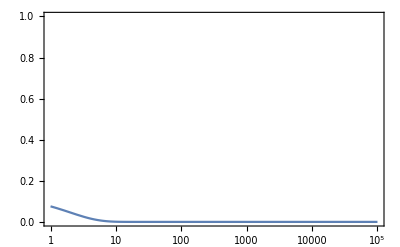

```mathematica
LogLinearPlot[fitsCRSISF[[1]][x],{x,1,100000},PlotRange->{Automatic,{0,1}}]
```

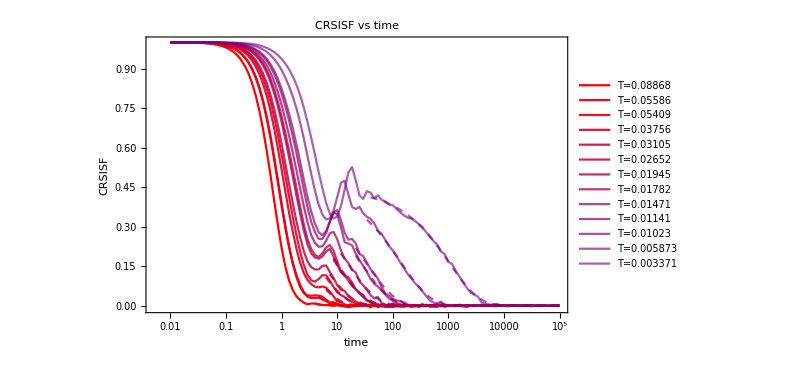

```mathematica
CRSISFfitST=Show[CRSISFPlot,Table[LogLinearPlot[fitsCRSISF[[T]][x],{x,time[[1]][[starttimeCRoverlap[[T]]]],100000},PlotRange->{{0.01,10000},{0,1}},PlotStyle->{Dashed,redBluePlotConfig[Length[TlistAllT]][[T]]}],{T,Length[Tlist]}]]
```

```mathematica
Export["/home/chengling/Downloads/CRSISF.jpeg",Show[CRSISFPlot,Table[LogLinearPlot[fitsCRSISF[[T]][x],{x,time[[1]][[starttimeCRoverlap[[T]]]],100000},PlotRange->{{0.01,10000},{0,1}},PlotStyle->{Dashed,redBluePlotConfig[Length[Tlist]][[T]]}],{T,Length[Tlist]}]],ImageResolution->600];
```

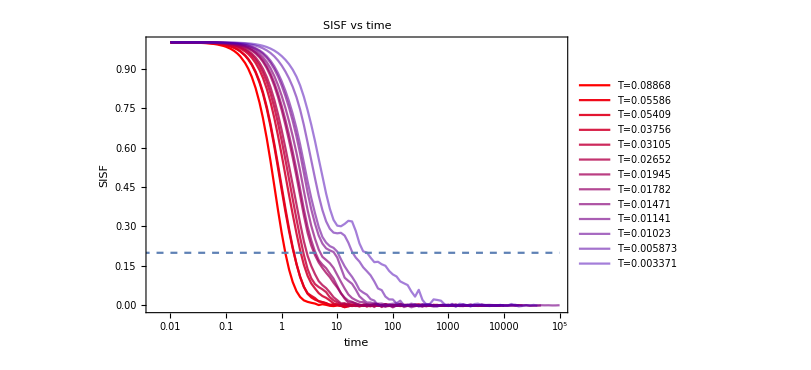

```mathematica
SISFPlot=ListLogLinearPlot[Table[Table[{time[[T,rec]],SISFMean[[T,rec]]},{rec,Length[SISFCRMean[[T]]]}],{T,Length[Tlist]}],PlotLegends->Table["T="<>ToString[Tlist[[T]]],{T,Length[Tlist]}],PlotStyle->redBluePlotConfig[Length[Tlist]+Length[TlistLT]],FrameLabel->{"time","SISF"},ImageSize->600,PlotLabel->"SISF vs time",Joined->True];
Show[SISFPlot,LogLinearPlot[0.2,{x,0.001,100000},PlotStyle->Dashed]]
```

```mathematica
tauSISF={1.1850304699280552, 1.6812343373278569, 1.6812343373278569, 2.2068443912378317, 2.4797312933736735, 2.8967777180178738, 3.8770147182394656, 4.190373397459676, 5.089099119455345, 8.94059964855107, 10.444248502589051, 19.449990370316907,34.17001182083235};
```

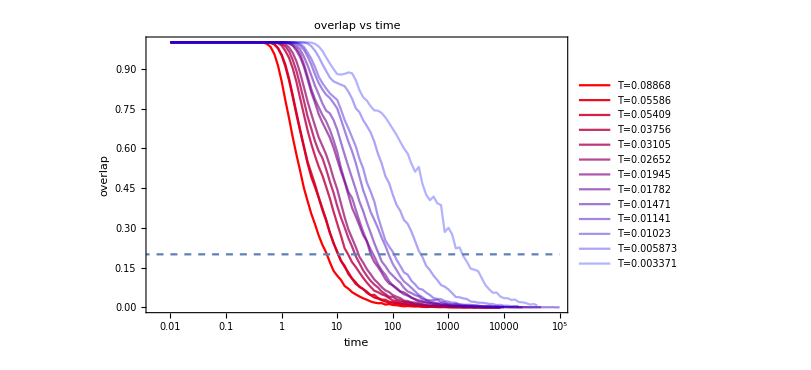

```mathematica
overlapPlot=ListLogLinearPlot[Table[Table[{time[[T,rec]],overlapMean[[T,rec]]},{rec,Length[overlapMean[[T]]]}],{T,Length[Tlist]}],PlotLegends->Table["T="<>ToString[Tlist[[T]]],{T,Length[Tlist]}],PlotStyle->redBluePlotConfig[Length[Tlist]],FrameLabel->{"time","overlap"},ImageSize->600,PlotLabel->"overlap vs time",Joined->True];
Show[overlapPlot,LogLinearPlot[0.2,{x,0.001,100000},PlotStyle->Dashed]]
```

```mathematica
tauOverlap={6.69331196409322,10.656254929592683,10.656254929592683,16.007469910413192,20.99512872389787,24.515441552631614,40.574181058301946,44.70018134539799,56.39944600532097,86.38220626423953,106.90325084427924,322.5925296227043,1809.7501730289523};
```

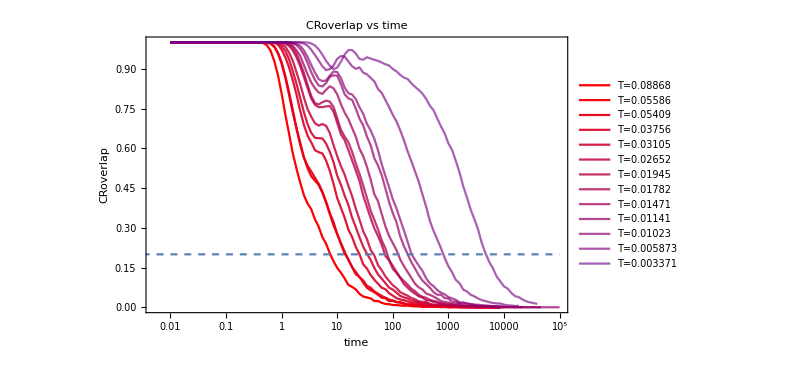

```mathematica
CRoverlapPlot=ListLogLinearPlot[Table[Table[{time[[T,rec]],overlapCRMean[[T,rec]]},{rec,Length[overlapMean[[T]]]}],{T,Length[Tlist]}],PlotLegends->Table["T="<>ToString[Tlist[[T]]],{T,Length[Tlist]}],PlotStyle->redBluePlotConfig[Length[TlistAllT]],FrameLabel->{"time","CRoverlap"},ImageSize->600,PlotLabel->"CRoverlap vs time",Joined->True];
Show[CRoverlapPlot,LogLinearPlot[0.2,{x,0.001,100000},PlotStyle->Dashed]]
```

```mathematica
starttimeNumerical={3.439670596624857,4.513301869539773,4.691895325598563,5.587158749116984,5.92204782213128,6.783606914108317,8.0779911081873,8.562178344582911,10,19.721676025502724,20.903774852301368,31.418902550272946,37.41396260774782};
```

```mathematica
position=Position[time[[1]],_?(#>starttimeNumerical[[1]]&),1,1][[1,1]]
```

34

```mathematica
time[[1]][[33]]
```

3.41

```mathematica
tauCRoverlap={7.588845266780288,13.848806946601167,14.678893807099623,25.2725476804456,35.83726260716043,45.2333443596138,72.05932171830304,79.40381775089199,128.97330949052682,186.478559663751,222.06075310279314,814.8545235206616,4856.943839235382};
```

```mathematica
starttimeCRoverlap=Table[Position[time[[1]],_?(#>starttimeNumerical[[T]]&),1,1][[1,1]],{T,Length[Tlist]}]
```

{34,35,36,37,37,38,39,39,41,45,45,48,49}

```mathematica
fitsCRoverlap=Table[NonlinearModelFit[Table[{Normal[time[[T,rec]]],Normal[overlapCRMean[[T,rec]]]},{rec,starttimeCRoverlap[[T]],Length[overlapMean[[T]]]}],{stretchedExp[t,G,τ,β],{0.8>β>0.1,1>G>0.1,τ>3}},{G,τ,β},t],{T,Length[Tlist]}];
```

```mathematica
Length[overlapCRMean[[7]]]
```

90

```mathematica
fitsCRoverlap
```

{FittedModel[0.999912 ⅇ^(-0.54396 t^0.529141)],FittedModel[0.999974 ⅇ^(-0.322458 t^0.592079)],FittedModel[0.999974 ⅇ^(-0.336738 t^0.569808)],FittedModel[0.999988 ⅇ^(-0.203059 t^0.630995)],FittedModel[0.999992 ⅇ^(-0.15971 t^0.641043)],FittedModel[0.999993 ⅇ^(-0.123769 t^0.665991)],FittedModel[0.999996 ⅇ^(-0.0796109 t^0.691322)],FittedModel[0.999996 ⅇ^(-0.0714166 t^0.701875)],FittedModel[0.999997 ⅇ^(-0.0529767 t^0.704992)],FittedModel[0.999996 ⅇ^(-0.0342643 t^0.729689)],FittedModel[0.999997 ⅇ^(-0.0281888 t^0.738498)],FittedModel[0.999998 ⅇ^(-0.00971697 t^0.762204)],FittedModel[0.980185 ⅇ^(-0.00245687 t^0.759353)]}

```mathematica
tauCRoverlapfits=Table[fitsCRoverlap[[T]]["BestFitParameters"][[2,2]],{T,Length[Tlist]}]
```

{3.16039,6.7635,6.75448,12.5106,17.4891,23.0389,38.8819,42.9591,64.5399,101.84,125.531,436.846,2732.95}

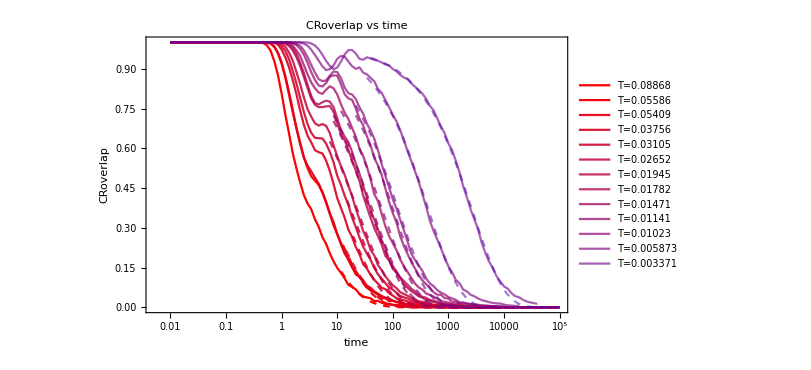

```mathematica
CRoverlapfitST=Show[CRoverlapPlot,Table[LogLinearPlot[fitsCRoverlap[[T]][x],{x,time[[1]][[starttimeCRoverlap[[T]]]],100000},PlotStyle->{Dashed,redBluePlotConfig[Length[Tlist]+Length[TlistLT]][[T]]}],{T,Length[Tlist]}]]
```

```mathematica
Export["/home/chengling/Downloads/CRoverlap.jpeg",Show[CRoverlapPlot,Table[LogLinearPlot[fitsCRoverlap[[T]][x],{x,starttimeNumerical[[T]],100000},PlotStyle->{Dashed,redBluePlotConfig[Length[Tlist]][[T]]}],{T,Length[Tlist]}]],ImageResolution->600];
```

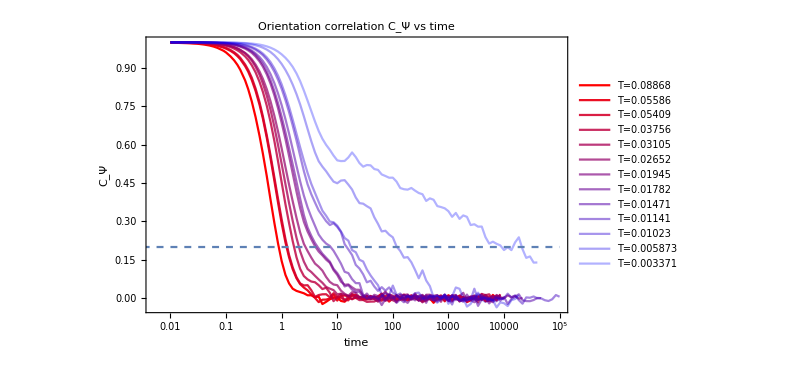

```mathematica
OCPlot=ListLogLinearPlot[Table[Table[{time[[T,rec]],orientationMeanReal[[T,rec]]},{rec,Length[orientationMeanReal[[T]]]}],{T,Length[Tlist]}],PlotLegends->Table["T="<>ToString[Tlist[[T]]],{T,Length[Tlist]}],PlotStyle->redBluePlotConfig[Length[Tlist]],FrameLabel->{"time","C_Ψ"},ImageSize->600,PlotLabel->"Orientation correlation C_Ψ vs time",Joined->True];
Show[OCPlot,LogLinearPlot[0.2,{x,0.001,100000},PlotStyle->Dashed]]
```

```mathematica
tauOrien={0.9067992308734952,1.213153170284103,1.2611076465299216,1.6872291282776422,2.0886741588110778,2.687950430419157,4.040057512579176,4.538886735048006,7.664387170407078,14.824985906248003,17.999645510533625,118.21693150965389,9305.28516988292};
```

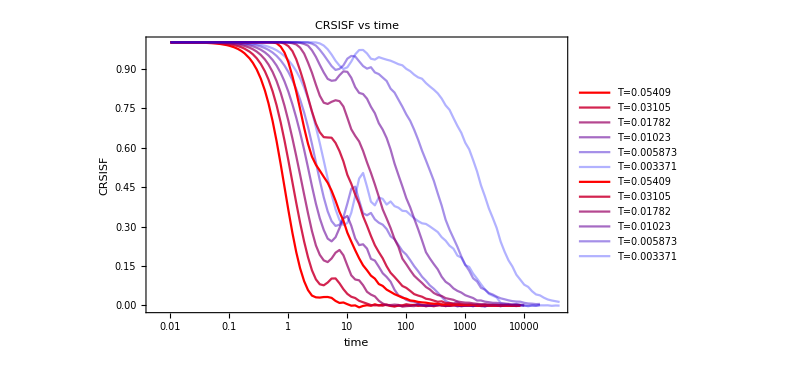

```mathematica
Show[CRSISFPlot,CRoverlapPlot]
```

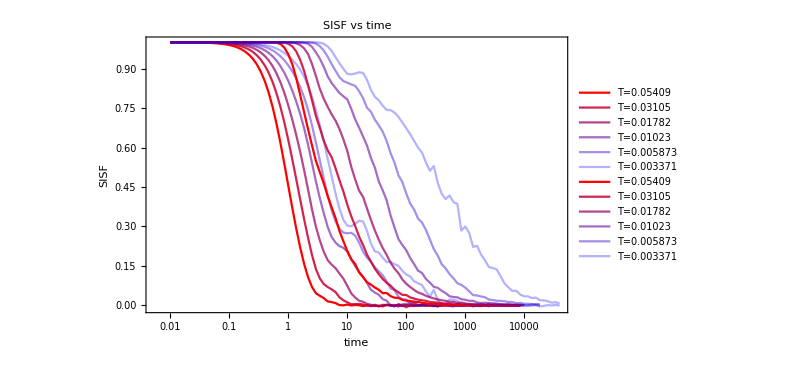

```mathematica
Show[SISFPlot,overlapPlot]
```

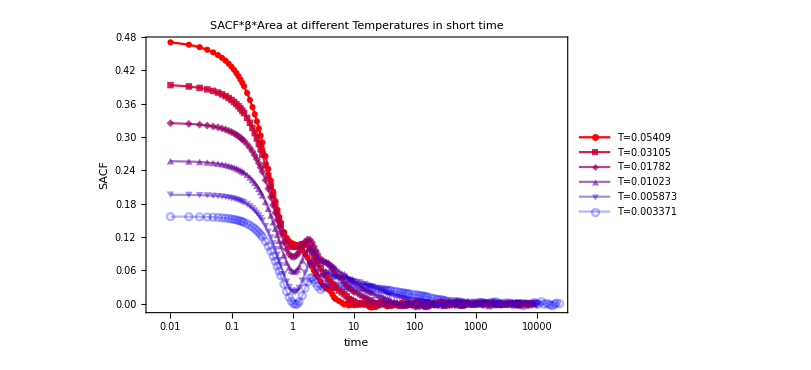

```mathematica
SACPlot=ListLogLinearPlot[Table[Table[{Normal[SAC[[T,1]][[2]]][[t]],Mean[Table[Normal[SAC[[T,id]][[1]]][[t]],{id,2}]]/Tlist[[T]]*4096},{t,Length[Normal[SAC[[T,1]][[2]]]]}],{T,Length[Tlist]}],PlotStyle->redBluePlotConfig[6],PlotLegends->Table[StringJoin["T=",ToString[Tlist[[T]]]],{T,Length[Tlist]}],FrameLabel->{"time","SACF"},ImageSize->600,PlotLabel->"SACF*β*Area at different Temperatures in short time",PlotMarkers->Automatic,Joined->True]
```

```mathematica
Normal[SAC[[1,2]][[1]]][[30]]/Tlist[[1]]*4096
```

0.18867

```mathematica
Normal[SAC[[1,1]][[2]]][[60]]
```

7.04

```mathematica
fit=NonlinearModelFit[Table[{Normal[SAC[[1,1]][[2]]][[t]],Mean[Table[Normal[SAC[[1,id]][[1]]][[t]],{id,2}]]/Tlist[[1]]*4096},{t,40,Length[Normal[SAC[[1,1]][[2]]]]}],{stretchedExp[t,G,τ,β],{β>0.01,G>0,τ>0}},{G,τ,β},t]
```

```mathematica
startT={50,50,50,55,60,60};
```

```mathematica
fits=Table[fit=NonlinearModelFit[Table[{Normal[SAC[[T,1]][[2]]][[t]],Mean[Table[Normal[SAC[[T,id]][[1]]][[t]],{id,2}]]/Tlist[[T]]*4096},{t,startT[[T]],Length[Normal[SAC[[T,1]][[2]]]]}],{stretchedExp[t,G,τ,β],{β>0.01,G>0,τ>0}},{G,τ,β},t],{T,Length[Tlist]}];
```

{FittedModel[0.0515714 ⅇ^(-0.0106612 t^3.12225)],FittedModel[0.150658 ⅇ^(-0.27176 t^1.10292)],FittedModel[0.156775 ⅇ^(-0.248541 t^0.890275)],FittedModel[0.133466 ⅇ^(-0.239298 t^0.693774)],FittedModel[0.0597813 ⅇ^(-0.0544068 t^0.846699)],FittedModel[0.0366357 ⅇ^(-0.0372609 t^0.670123)]}

```mathematica
fits[[1]]
```

FittedModel[0.0515714 ⅇ^(-0.0106612 t^3.12225)]

```mathematica
tauSAC=Table[fits[[T]]["BestFitParameters"][[2,2]],{T,Length[Tlist]}]
```

{4.28211,3.25847,4.77658,7.85582,31.1363,135.54}

```mathematica
tauSAC={4.282105359615349,3.2584666641154687,4.776583174333305,7.855817747832287,31.136260249519534,135.5398610921904};
```

```mathematica
fit["BestFitParameters"]
```

{G→0.164878,τ→2.26887,β→1.30963}

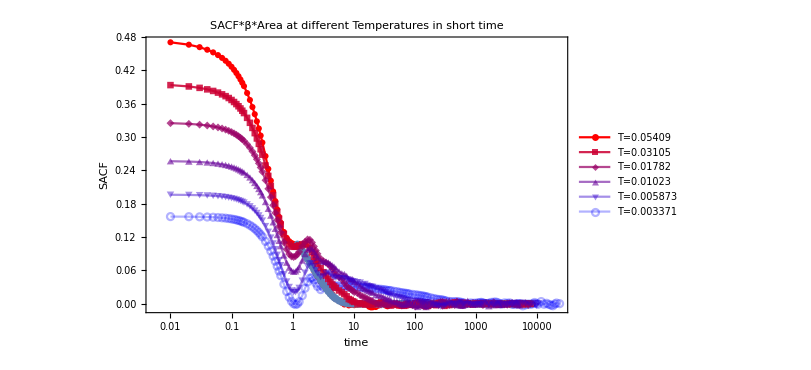

```mathematica
Show[SACPlot,fitPlot]
```

General::munfl: Exp[-785.796] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-902.059] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1021.98] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

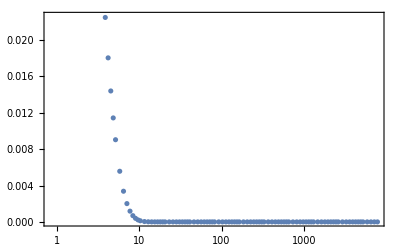

```mathematica
fitPlot=ListLogLinearPlot[Table[{Normal[SAC[[1,1]][[2]][[rec]]],fit[Normal[SAC[[2,1]][[2]][[rec]]]]},{rec,40,Length[Normal[SAC[[2,1]][[2]]]]}]]
```

```mathematica
overlapCRSSIF[[1,1,1,1]]
```

1.

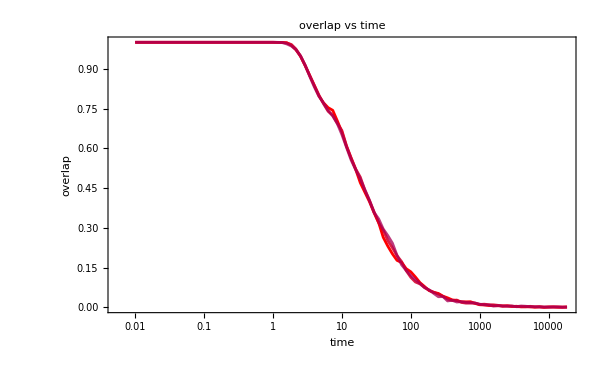

```mathematica
ListLogLinearPlot[Table[Table[{time[[6,rec]],overlapCRSSIF[[6,i,1,rec]]},{rec,Length[CRSISF[[6]]]}],{i,3}],PlotStyle->redBluePlotConfig[Length[Tlist]],FrameLabel->{"time","overlap"},ImageSize->600,PlotLabel->"overlap vs time",Joined->True]
```

```mathematica
TauAol={6.656916336382439,
10.532655112230382,
17.261092293760527,
25.00279850043277,
40.26115307072112,
61.488680836669154,
85.97848233539733}
```

{6.65692,10.5327,17.2611,25.0028,40.2612,61.4887,85.9785}

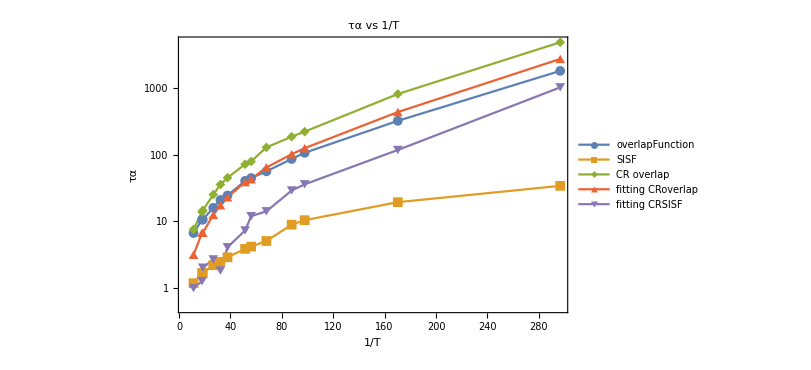

```mathematica
tauAlphaPlot=ListLogPlot[{Table[{1/Tlist[[T]],tauOverlap[[T]]},{T,Length[Tlist]}],Table[{1/Tlist[[T]],tauSISF[[T]]},{T,Length[Tlist]}],Table[{1/Tlist[[T]],tauCRoverlap[[T]]},{T,Length[Tlist]}],Table[{1/Tlist[[T]],tauCRoverlapfits[[T]]},{T,Length[Tlist]}],Table[{1/Tlist[[T]],tauCRSISFfits[[T]]},{T,Length[Tlist]}]},FrameLabel->{"1/T","τα"},PlotLegends->{"overlapFunction","SISF","CR overlap", "fitting CRoverlap","fitting CRSISF"},PlotMarkers->{Automatic,Medium},ImageSize->600,PlotLabel->"τα vs 1/T",Joined->True,PlotRange->All]
```

```mathematica
Export["/home/chengling/Downloads/tauAlpha.jpeg",tauAlphaPlot,ImageResolution->600];
```

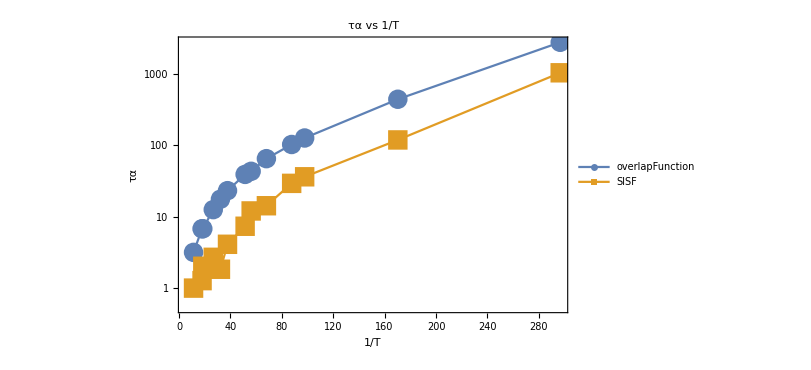

```mathematica
tauAlphafitingPlot=ListLogPlot[{Table[{1/Tlist[[T]],tauCRoverlapfits[[T]]},{T,Length[Tlist]}],Table[{1/Tlist[[T]],tauCRSISFfits[[T]]},{T,Length[Tlist]}]},FrameLabel->{"1/T","τα"},PlotLegends->{"overlapFunction","SISF","Orientation","Stress Auto-correlation","CR overlap"},PlotMarkers->{Automatic,Large},ImageSize->600,PlotLabel->"τα vs 1/T",Joined->True,PlotRange->All]
```

```mathematica
Export["/home/chengling/Research/Project/Cell/update/01252024/CRSISF.jpeg",Show[CRSISFPlot,LogLinearPlot[0.2,{x,0.001,100000},PlotStyle->Dashed]],ImageResolution->600];
Export["/home/chengling/Research/Project/Cell/update/01252024/SISF.jpeg",Show[SISFPlot,LogLinearPlot[0.2,{x,0.001,100000},PlotStyle->Dashed]],ImageResolution->600];
Export["/home/chengling/Research/Project/Cell/update/01252024/overlap.jpeg",Show[overlapPlot,LogLinearPlot[0.2,{x,0.001,100000},PlotStyle->Dashed]],ImageResolution->600];Export["/home/chengling/Research/Project/Cell/update/01252024/CRoverlap.jpeg",Show[CRoverlapPlot,LogLinearPlot[0.2,{x,0.001,100000},PlotStyle->Dashed]],ImageResolution->600];
Export["/home/chengling/Research/Project/Cell/update/01252024/OC.jpeg",Show[OCPlot,LogLinearPlot[0.2,{x,0.001,100000},PlotStyle->Dashed]],ImageResolution->600];
Export["/home/chengling/Downloads/tauAlpha.jpeg",tauAlphaPlot,ImageResolution->600];Export["/home/chengling/Research/Project/Cell/update/01252024/SAC.jpeg",Show[SACPlot,fitPlot],ImageResolution->600];
```

```mathematica
(*Fit the last 3 data points of CRSISFfit, and predict low T with their Tau\alpha*)
```

```mathematica
fitting=LinearModelFit[Table[{1/Tlist[[T]],Log10[tauCRSISFfits[[T]]]},{T,Length[Tlist]-2,Length[Tlist]}],x,x]
```

FittedModel[0.834324+0.00732316 x]

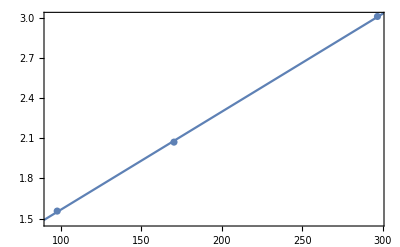

```mathematica
Show[ListPlot[Table[{1/Tlist[[T]],Log10[tauCRSISFfits[[T]]]},{T,Length[Tlist]-2,Length[Tlist]}]],Plot[fitting[x],{x,50,400}]]
```

```mathematica
Table[Solve[fitting[x]==3+i/5,x],{i,5}]
```

{{{x→323.04}},{{x→350.351}},{{x→377.661}},{{x→404.972}},{{x→432.283}}}

```mathematica
1/Table[Solve[fitting[x]==3+i/5,x][[1,1,2]],{i,5}]
```

{0.00309559,0.00285428,0.00264787,0.00246931,0.0023133}

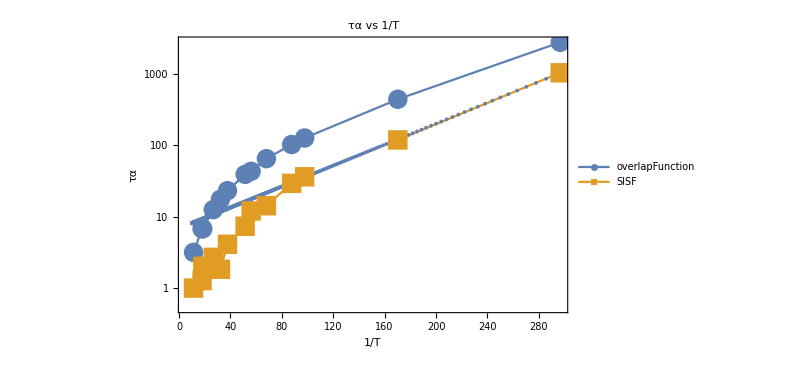

```mathematica
Show[tauAlphafitingPlot,ListLogPlot[Table[{1/T,10^fitting[1/T]},{T,0.0001,0.1,0.0001}]]]
```

## longer times when τα belongs (1000,10000)

### check if we equilibrate long enough

```mathematica
saveFolderLT="/home/chengling/Research/Project/Cell/glassyDynamics/longtimeSimulation/N4096/";
```

```mathematica
TlistLT={0.00309559, 0.00285428, 0.00264787 ,0.00246931, 0.0023133};
```

```mathematica
1/TlistLT
```

{323.04,350.351,377.662,404.971,432.283}

```mathematica
N[1/{450,475,500,525,550}]
```

{0.00222222,0.00210526,0.002,0.00190476,0.00181818}

```mathematica
TstringLT=ToString[NumberForm[#,{9,8},ExponentFunction->(Null&)]]&/@TlistLT
```

{0.00309559,0.00285428,0.00264787,0.00246931,0.00231330}

```mathematica
wtlistLT={100.,316.22,1000.,3162.27,10000.,31622.77,100000.};
```

```mathematica
wtliststringLT=ToString[NumberForm[#,{9,6},ExponentFunction->(Null&)]]&/@wtlistLT
```

{100.000000,316.220000,1000.000000,3162.270000,10000.000000,31622.770000,100000.000000}

```mathematica
SISFLT=Table[Table[Import[StringJoin[saveFolderLT,"SISF_N4096_p3.8000_T",TstringLT[[5]],"_waitingTime",wtliststringLT[[wt]],"_idx",ToString[idx],".nc"],"Data"],{wt,7}],{idx,0,2}];
```

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/longtimeSimulation/N4096/SISF_N4096_p3.8000_T0.00231330_waitingTime100.000000_idx0.nc not found during Import.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/longtimeSimulation/N4096/SISF_N4096_p3.8000_T0.00231330_waitingTime316.220000_idx0.nc not found during Import.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/longtimeSimulation/N4096/SISF_N4096_p3.8000_T0.00231330_waitingTime1000.000000_idx0.nc not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

```mathematica
overlapLT=Table[Table[Import[StringJoin[saveFolderLT,"overlap_N4096_p3.8000_T",TstringLT[[5]],"_waitingTime",wtliststringLT[[wt]],"_idx",ToString[idx],".nc"],"Data"],{wt,7}],{idx,0,2}];
```

```mathematica
SISFLT[[1,1,1]]
```

1.

```mathematica
timeLT=Table[testdata=Import[StringJoin[saveFolderLT,"glassyDynamics_N4096_p3.8000_T",TstringLT[[2]],"_waitingTime",wtliststringLT[[wt]],"_idx1.nc"],"Data"];Table[testdata[[4,j,1]]-testdata[[4,1,1]],{j,Length[testdata[[4]]]}],{wt,7}];
```

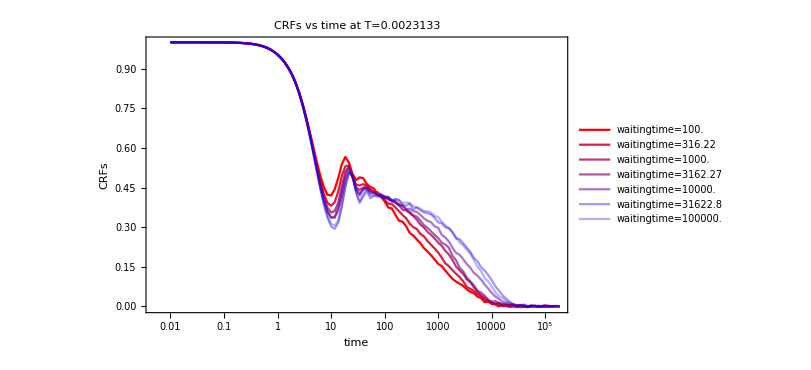

```mathematica
CRFswaitTimeLT=ListLogLinearPlot[Table[Table[{timeLT[[wt,t]],Mean[Table[SISFLT[[idx,wt,2,t]],{idx,3}]]},{t,Length[timeLT[[wt]]]}],{wt,7}],FrameLabel->{"time","CRFs"},ImageSize->600,PlotLabel->"CRFs vs time at T=0.0023133",Joined->True,PlotStyle->redBluePlotConfig[7],PlotLegends->Table["waitingtime="<>ToString[wtlistLT[[wt]]],{wt,7}]]
```

```mathematica
Export["/home/chengling/Research/updates/02012024/CRFswaitTimeLT.jpeg",CRFswaitTimeLT,ImageResolution->600];
```

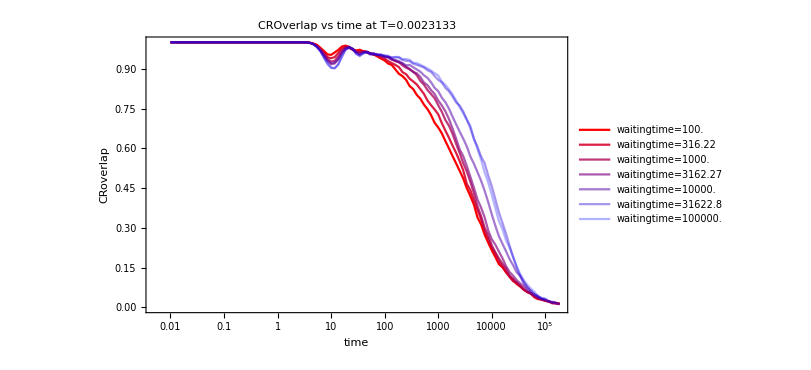

```mathematica
CRoverlapwaitTimeLT=ListLogLinearPlot[Table[Table[{timeLT[[wt,t]],Mean[Table[overlapLT[[idx,wt,2,t]],{idx,3}]]},{t,Length[timeLT[[wt]]]}],{wt,7}],FrameLabel->{"time","CRoverlap"},ImageSize->600,PlotLabel->"CROverlap vs time at T=0.0023133",Joined->True,PlotStyle->redBluePlotConfig[7],PlotLegends->Table["waitingtime="<>ToString[wtlistLT[[wt]]],{wt,7}]]
```

```mathematica
Export["/home/chengling/Research/updates/02012024/CRoverlapwaitTimeLT.jpeg",CRoverlapwaitTimeLT,ImageResolution->600];
```

### the relaxation time for these low temperature

```mathematica
overlapLT=Table[Table[Import[StringJoin[saveFolderLT,"overlap_N4096_p3.8000_T",TstringLT[[T]],"_waitingTime100000.000000_idx",ToString[i],".nc"],"Data"],{i,0,2}],{T,Length[TlistLT]}];
```

```mathematica
SISFLT=Table[Table[Import[StringJoin[saveFolderLT,"SISF_N4096_p3.8000_T",TstringLT[[T]],"_waitingTime100000.000000_idx",ToString[i],".nc"],"Data"],{i,0,2}],{T,Length[TlistLT]}];
```

```mathematica
CRoverlapMeanLT=Table[Table[Mean[Table[overlapLT[[T,i,2,rec]],{i,3}]],{rec,Length[overlapLT[[T,1,1]]]}],{T,Length[TlistLT]}];
```

```mathematica
CRSISFMeanLT=Table[Table[Mean[Table[SISFLT[[T,i,2,rec]],{i,3}]],{rec,Length[SISFLT[[T,1,1]]]}],{T,Length[TlistLT]}];
```

```mathematica
testdata=Import[StringJoin[saveFolderLT,"glassyDynamics_N4096_p3.8000_T",TstringLT[[2]],"_waitingTime",wtliststringLT[[7]],"_idx1.nc"],"Data"];timeLT=Table[testdata[[4,j,1]]-testdata[[4,1,1]],{j,Length[testdata[[4]]]}]
```

{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.09,0.1,0.12,0.14,0.16,0.18,0.22,0.25,0.29,0.34,0.4,0.46,0.54,0.63,0.74,0.86,1.,1.17,1.36,1.58,1.85,2.15,2.51,2.93,3.41,3.98,4.64,5.41,6.31,7.36,8.58,10.,11.66,13.59,15.85,18.48,21.54,25.12,29.29,34.15,39.81,46.42,54.12,63.1,73.56,85.77,100.,116.59,135.94,158.49,184.78,215.44,251.19,292.86,341.45,398.11,464.16,541.17,630.96,735.64,857.7,1000.,1165.91,1359.36,1584.89,1847.85,2154.43,2511.89,2928.64,3414.55,3981.07,4641.59,5411.7,6309.57,7356.42,8576.96,10000.,11659.1,13593.6,15848.9,18478.5,21544.3,25118.9,29286.4,34145.5,39810.7,46415.9,54117.,63095.7,73564.2,85769.6,100000.}

```mathematica
CRoverlapMeanLT[[1,50]]
```

0.942952

```mathematica
Log10[timeLT[[52]]]
```

1.80003

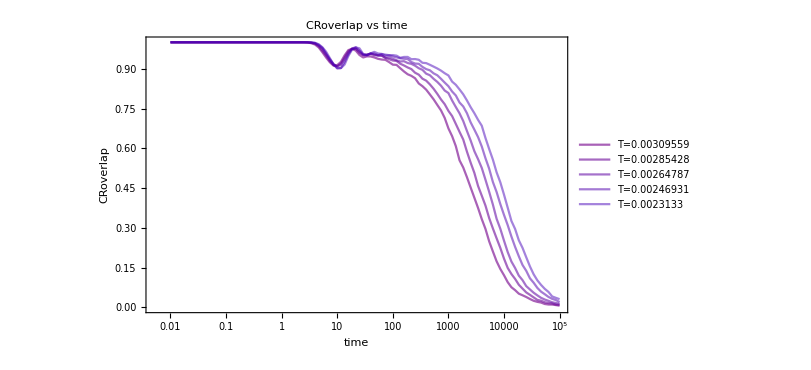

```mathematica
CRoverlapLTPlot=ListLogLinearPlot[Table[Table[{timeLT[[rec]],CRoverlapMeanLT[[T,rec]]},{rec,Length[CRoverlapMeanLT[[T]]]}],{T,Length[TlistLT]}],PlotLegends->Table["T="<>ToString[TlistLT[[T]]],{T,Length[TlistLT]}],PlotStyle->redBluePlotConfig[Length[TlistAllT]][[Length[Tlist];;]],FrameLabel->{"time","CRoverlap"},ImageSize->600,PlotLabel->"CRoverlap vs time",Joined->True]
```

```mathematica
Table[{Normal[timeLT[[rec]]],Normal[CRoverlapMeanLT[[2,rec]]]},{rec,52,Length[timeLT]}]
```

{{63.1,0.949707},{73.56,0.941406},{85.77,0.936279},{100.,0.931234},{116.59,0.929688},{135.94,0.919189},{158.49,0.912679},{184.78,0.905111},{215.44,0.898926},{251.19,0.885254},{292.86,0.87793},{341.45,0.86263},{398.11,0.855306},{464.16,0.841227},{541.17,0.824707},{630.96,0.80542},{735.64,0.784424},{857.7,0.766439},{1000.,0.741292},{1165.91,0.72168},{1359.36,0.691976},{1584.89,0.662191},{1847.85,0.633219},{2154.43,0.587484},{2511.89,0.545898},{2928.64,0.507406},{3414.55,0.457926},{3981.07,0.421387},{4641.59,0.38387},{5411.7,0.33667},{6309.57,0.29777},{7356.42,0.260661},{8576.96,0.224447},{10000.,0.183919},{11659.1,0.148682},{13593.6,0.125732},{15848.9,0.107178},{18478.5,0.0852051},{21544.3,0.0707194},{25118.9,0.0563965},{29286.4,0.0471191},{34145.5,0.0375163},{39810.7,0.0280762},{46415.9,0.0249837},{54117.,0.0192871},{63095.7,0.0161133},{73564.2,0.0146484},{85769.6,0.0102539},{100000.,0.00976563}}

```mathematica
fitsCRoverlapLT=Table[NonlinearModelFit[Table[{Normal[timeLT[[rec]]],Normal[CRoverlapMeanLT[[T,rec]]]},{rec,52,Length[timeLT]}],{stretchedExp[t,G,τ,β],{0.81>β>0.2,1>G>0,τ>3}},{G,τ,β},t],{T,Length[TlistLT]}];
```

```mathematica
fitsCRoverlapLT
```

{FittedModel[0.993608 ⅇ^(-0.00252691 t^0.730815)],FittedModel[0.988459 ⅇ^(-0.00175196 t^0.74279)],FittedModel[0.976593 ⅇ^(-0.000865638 t^0.794476)],FittedModel[0.980814 ⅇ^(-0.000874528 t^0.764024)],FittedModel[0.978599 ⅇ^(-0.000527407 t^0.795187)]}

```mathematica
tauCRoverlapfitsLT=Table[fitsCRoverlapLT[[T]]["BestFitParameters"][[2,2]],{T,Length[TlistLT]}]
```

{3582.02,5140.15,7160.55,10064.4,13246.9}

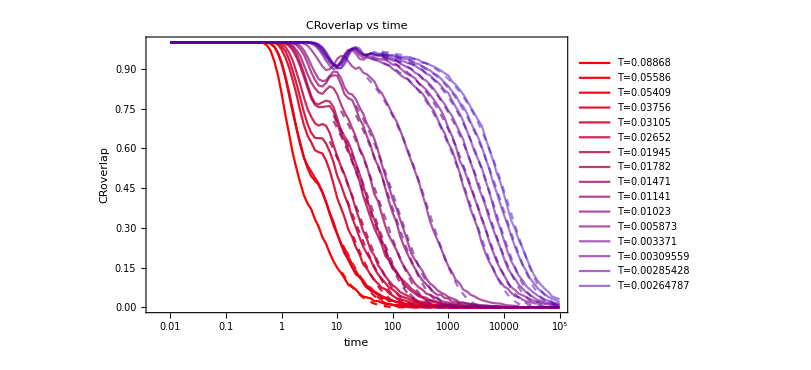

```mathematica
CRoverlapSTLTwithFitPlot=Show[CRoverlapfitST,CRoverlapLTPlot,Table[LogLinearPlot[fitsCRoverlapLT[[T]][x],{x,timeLT[[52]],100000},PlotRange->{{0.01,10000},{0,1}},PlotStyle->{Dashed,redBluePlotConfig[Length[TlistAllT]][[T+Length[Tlist]]]}],{T,Length[TlistLT]}]]
```

```mathematica
Export["/home/chengling/Research/updates/02012024/CRoverlap.jpeg",Show[CRoverlapfitST,CRoverlapLTPlot,Table[LogLinearPlot[fitsCRoverlapLT[[T]][x],{x,timeLT[[52]],100000},PlotRange->{{0.01,10000},{0,1}},PlotStyle->{Dashed,redBluePlotConfig[Length[Tlist]+Length[TlistLT]][[T+Length[Tlist]]]}],{T,Length[TlistLT]}]],ImageResolution->600];
```

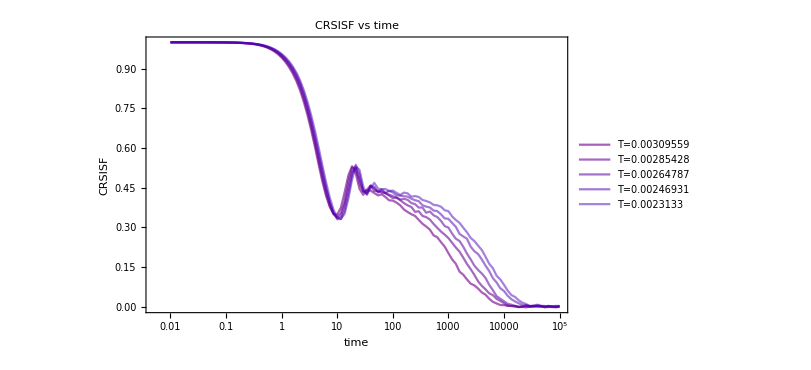

```mathematica
CRSISFLTPlot=ListLogLinearPlot[Table[Table[{timeLT[[rec]],CRSISFMeanLT[[T,rec]]},{rec,Length[CRoverlapMeanLT[[T]]]}],{T,Length[TlistLT]}],PlotLegends->Table["T="<>ToString[TlistLT[[T]]],{T,Length[TlistLT]}],PlotStyle->redBluePlotConfig[Length[TlistAllT]][[Length[Tlist];;]],FrameLabel->{"time","CRSISF"},ImageSize->600,PlotLabel->"CRSISF vs time",Joined->True]
```

```mathematica
fitsCRSISFLT=Table[NonlinearModelFit[Table[{Normal[timeLT[[rec]]],Normal[CRSISFMeanLT[[T,rec]]]},{rec,52,Length[timeLT]}],{stretchedExp[t,G,τ,β],{0.81>β>0.2,0.5>G>0,τ>3}},{G,τ,β},t],{T,Length[TlistLT]}];
```

```mathematica
fitsCRSISFLT[[1]]["BestFitParameters"]
```

{G→0.473171,τ→1239.22,β→0.703551}

```mathematica
tauCRSISFfitsLT=Table[fitsCRSISFLT[[T]]["BestFitParameters"][[2,2]],{T,Length[TlistLT]}]
```

{1239.22,2019.54,2804.8,4144.73,5262.53}

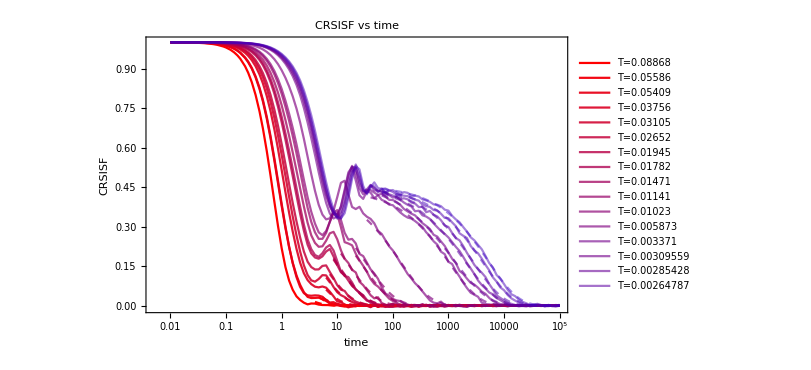

```mathematica
CRSISFSTLTwithFitPlot=Show[CRSISFfitST,CRSISFLTPlot,Table[LogLinearPlot[fitsCRSISFLT[[T]][x],{x,timeLT[[52]],100000},PlotRange->{{0.01,10000},{0,1}},PlotStyle->{Dashed,redBluePlotConfig[Length[TlistAllT]][[T+Length[Tlist]]]}],{T,Length[TlistLT]}]]
```

```mathematica
Export["/home/chengling/Research/updates/02012024/CRSISF.jpeg",Show[CRSISFfitST,CRSISFLTPlot,Table[LogLinearPlot[fitsCRSISFLT[[T]][x],{x,timeLT[[52]],100000},PlotRange->{{0.01,10000},{0,1}},PlotStyle->{Dashed,redBluePlotConfig[Length[Tlist]+Length[TlistLT]][[T+Length[Tlist]]]}],{T,Length[TlistLT]}]],ImageResolution->600];
```

```mathematica
tauCRoverlapAllT=Join[tauCRoverlapfits,tauCRoverlapfitsLT]
```

{3.1604,6.76348,6.75449,12.5106,17.4891,23.0389,38.8818,42.9591,64.5399,101.84,125.531,436.844,2732.95,3582.03,5140.15,7160.57,10064.4,13246.9}

```mathematica
tauCRSISFAllT=Join[tauCRSISFfits,tauCRSISFfitsLT]
```

{1.00003,1.2722,2.02152,2.69488,1.83521,4.09904,7.32571,11.9895,14.1807,29.1376,36.0037,117.905,1023.92,1191.37,1967.85,2784.07,4043.04,5209.9}

```mathematica
TlistAllT=Join[Tlist,TlistLT];
```

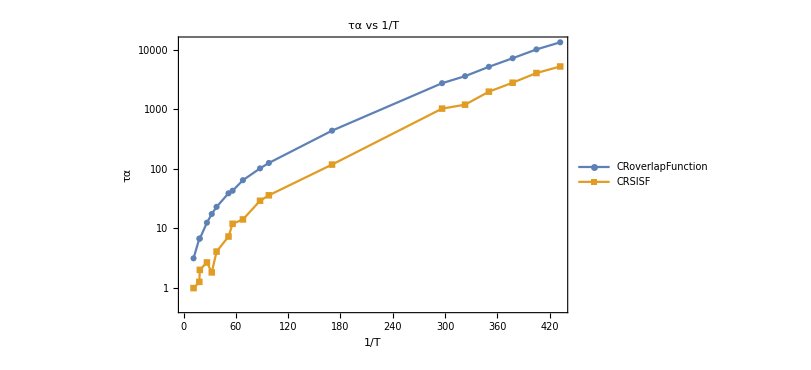

```mathematica
tauAlphafitingPlot=ListLogPlot[{Table[{1/TlistAllT[[T]],tauCRoverlapAllT[[T]]},{T,Length[TlistAllT]}],Table[{1/TlistAllT[[T]],tauCRSISFAllT[[T]]},{T,Length[TlistAllT]}]},FrameLabel->{"1/T","τα"},PlotLegends->{"CRoverlapFunction","CRSISF"},PlotMarkers->{Automatic},ImageSize->600,PlotLabel->"τα vs 1/T",Joined->True,PlotRange->All]
```

```mathematica
Export["/home/chengling/Research/updates/02012024/taualpha.jpeg",tauAlphafitingPlot,ImageResolution->600];
```

```mathematica
betaCRSISFfitsAllT=Join[Table[fitsCRSISF[[T]]["BestFitParameters"][[3,2]],{T,Length[Tlist]}],Table[fitsCRSISFLT[[T]]["BestFitParameters"][[3,2]],{T,Length[TlistLT]}]]
```

{0.799985,0.769502,0.785974,0.79955,0.65192,0.781039,0.768413,0.799486,0.799107,0.799858,0.799925,0.792635,0.799933,0.694171,0.763164,0.841017,0.805519,0.85376}

```mathematica
GCRSISFfitsAllT=Join[Table[fitsCRSISF[[T]]["BestFitParameters"][[1,2]],{T,Length[Tlist]}],Table[fitsCRSISFLT[[T]]["BestFitParameters"][[3,2]],{T,Length[TlistLT]}]]
```

{0.255671,0.656584,0.770021,0.997755,0.973854,0.575983,0.506013,0.472672,0.496051,0.453602,0.473991,0.461315,0.417662,0.694171,0.763164,0.841017,0.805519,0.85376}

```mathematica
betaCRoverlapfitsAllT=Join[Table[fitsCRoverlap[[T]]["BestFitParameters"][[3,2]],{T,Length[Tlist]}],Table[fitsCRoverlapLT[[T]]["BestFitParameters"][[3,2]],{T,Length[TlistLT]}]]
```

{0.529142,0.592079,0.569809,0.630995,0.641044,0.665992,0.691323,0.701876,0.704993,0.72969,0.738499,0.762203,0.759354,0.81093,0.819005,0.854924,0.831909,0.862638}

```mathematica
GCRoverlapfitsAllT=Join[Table[fitsCRoverlap[[T]]["BestFitParameters"][[1,2]],{T,Length[Tlist]}],Table[fitsCRoverlapLT[[T]]["BestFitParameters"][[3,2]],{T,Length[TlistLT]}]]
```

{0.999912,0.999975,0.999973,0.999988,0.999992,0.999993,0.999996,0.999996,0.999997,0.999996,0.999997,1.,0.980185,0.730817,0.742792,0.794486,0.764026,0.795196}

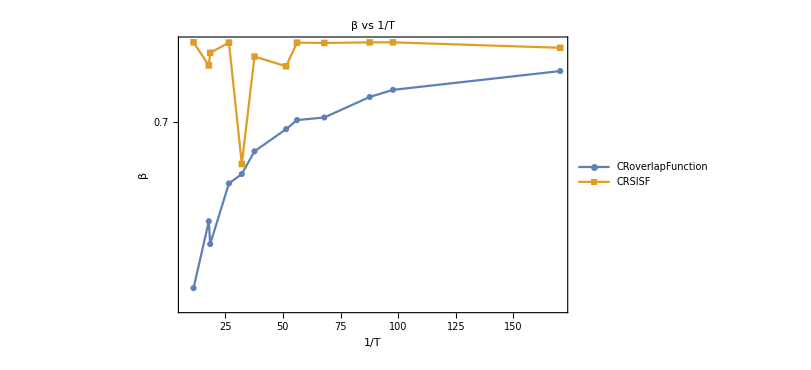

```mathematica
betafitingPlot=ListLogPlot[{Table[{1/TlistAllT[[T]],betaCRoverlapfitsAllT[[T]]},{T,12}],Table[{1/TlistAllT[[T]],betaCRSISFfitsAllT[[T]]},{T,12}]},FrameLabel->{"1/T","β"},PlotLegends->{"CRoverlapFunction","CRSISF"},PlotMarkers->{Automatic},ImageSize->600,PlotLabel->"β vs 1/T",Joined->True,PlotRange->All]
```

```mathematica
Export["/home/chengling/Research/updates/02012024/beta.jpeg",betafitingPlot,ImageResolution->600];
```

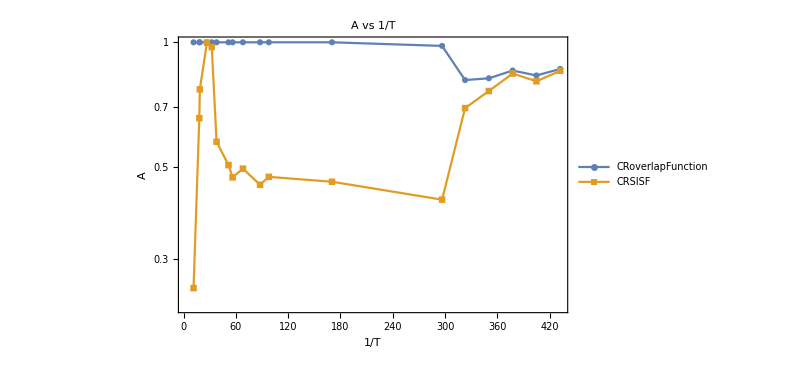

```mathematica
GfitingPlot=ListLogPlot[{Table[{1/TlistAllT[[T]],GCRoverlapfitsAllT[[T]]},{T,18}],Table[{1/TlistAllT[[T]],GCRSISFfitsAllT[[T]]},{T,18}]},FrameLabel->{"1/T","A"},PlotLegends->{"CRoverlapFunction","CRSISF"},PlotMarkers->{Automatic},ImageSize->600,PlotLabel->"A vs 1/T",Joined->True,PlotRange->All]
```

```mathematica
Export["/home/chengling/Research/updates/02012024/A.jpeg",GfitingPlot,ImageResolution->600];
```

## longest times when τα belongs (1000,10000)

### check if we equilibrate long enough

```mathematica
saveFolderLT="/home/chengling/Research/Project/Cell/glassyDynamics/longtimeSimulation/N4096/";
```

```mathematica
TlistLongest={0.00222222 ,0.00210526, 0.002, 0.00190476 ,0.00181818};
```

```mathematica
1/TlistLongest
```

{450.,475.001,500.,525.001,550.001}

```mathematica
N[1/{450,475,500,525,550}]
```

{0.00222222,0.00210526,0.002,0.00190476,0.00181818}

```mathematica
TstringLongest=ToString[NumberForm[#,{9,8},ExponentFunction->(Null&)]]&/@TlistLongest
```

{0.00222222,0.00210526,0.00200000,0.00190476,0.00181818}

```mathematica
wtlistLongest={0.,50000.,60000.,70000.,80000.,90000.,100000.};
```

```mathematica
wtliststringLongest=ToString[NumberForm[#,{9,6},ExponentFunction->(Null&)]]&/@wtlistLongest
```

{0.000000,50000.000000,60000.000000,70000.000000,80000.000000,90000.000000,100000.000000}

```mathematica
SISFLongest=Table[Table[Import[StringJoin[saveFolderLT,"SISF_N4096_p3.8000_T",TstringLongest[[1]],"_waitingTime",wtliststringLongest[[wt]],"_idx",ToString[idx],".nc"],"Data"],{wt,7}],{idx,0,2}];
```

```mathematica
overlapLongest=Table[Table[Import[StringJoin[saveFolderLT,"overlap_N4096_p3.8000_T",TstringLongest[[5]],"_waitingTime",wtliststringLongest[[wt]],"_idx",ToString[idx],".nc"],"Data"],{wt,7}],{idx,0,2}];
```

```mathematica
SISFLT[[1,1,1]]
```

1.

```mathematica
timeLongest=Table[testdata=Import[StringJoin[saveFolderLT,"glassyDynamics_N4096_p3.8000_T",TstringLongest[[2]],"_waitingTime",wtliststringLongest[[wt]],"_idx1.nc"],"Data"];Table[testdata[[4,j,1]]-testdata[[4,1,1]],{j,Length[testdata[[4]]]}],{wt,7}];
```

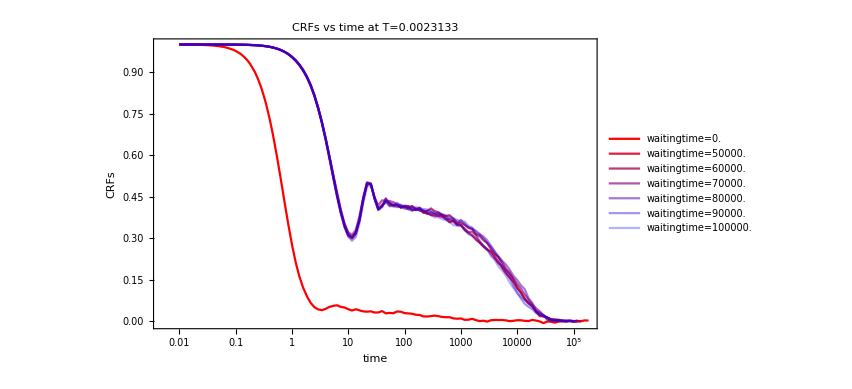

```mathematica
CRFswaitTimeLongest=ListLogLinearPlot[Table[Table[{timeLongest[[wt,t]],Mean[Table[SISFLongest[[idx,wt,2,t]],{idx,3}]]},{t,Length[timeLongest[[wt]]]}],{wt,7}],FrameLabel->{"time","CRFs"},ImageSize->600,PlotLabel->"CRFs vs time at T=0.0023133",Joined->True,PlotStyle->redBluePlotConfig[7],PlotLegends->Table["waitingtime="<>ToString[wtlistLongest[[wt]]],{wt,7}]]
```

```mathematica
Export["/home/chengling/Research/updates/02012024/CRFswaitTimeLT.jpeg",CRFswaitTimeLT,ImageResolution->600];
```

General::stop: Further output of Part::partw will be suppressed during this calculation.

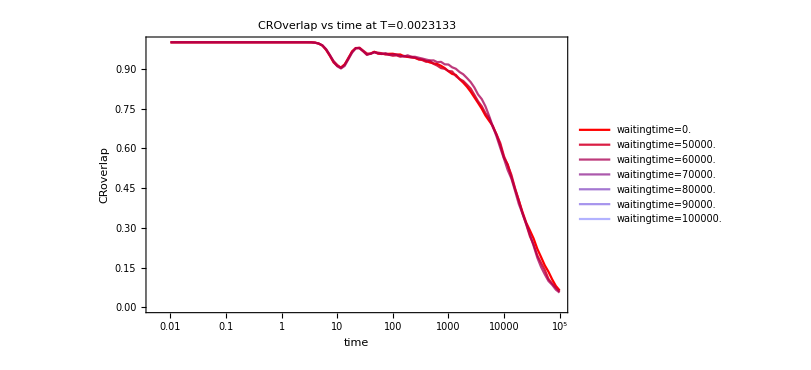

```mathematica
CRoverlapwaitTimeLongest=ListLogLinearPlot[Table[Table[{timeLongest[[t]],Mean[Table[overlapLongest[[idx,wt,2,t]],{idx,3}]]},{t,Length[timeLongest]}],{wt,7}],FrameLabel->{"time","CRoverlap"},ImageSize->600,PlotLabel->"CROverlap vs time at T=0.0023133",Joined->True,PlotStyle->redBluePlotConfig[7],PlotLegends->Table["waitingtime="<>ToString[wtlistLongest[[wt]]],{wt,7}]]
```

```mathematica
Export["/home/chengling/Research/updates/02012024/CRoverlapwaitTimeLT.jpeg",CRoverlapwaitTimeLT,ImageResolution->600];
```

### the relaxation time for these low temperature

```mathematica
overlapLongest=Table[Table[Import[StringJoin[saveFolderLT,"overlap_N4096_p3.8000_T",TstringLongest[[T]],"_waitingTime100000.000000_idx",ToString[i],".nc"],"Data"],{i,0,2}],{T,Length[TlistLongest]}];
```

```mathematica
SISFLongest=Table[Table[Import[StringJoin[saveFolderLT,"SISF_N4096_p3.8000_T",TstringLongest[[T]],"_waitingTime100000.000000_idx",ToString[i],".nc"],"Data"],{i,0,2}],{T,Length[TlistLongest]}];
```

```mathematica
CRoverlapMeanLongest=Table[Table[Mean[Table[overlapLongest[[T,i,2,rec]],{i,3}]],{rec,Length[overlapLongest[[T,1,1]]]}],{T,Length[TlistLongest]}];
```

```mathematica
CRSISFMeanLongest=Table[Table[Mean[Table[SISFLongest[[T,i,2,rec]],{i,3}]],{rec,Length[SISFLongest[[T,1,1]]]}],{T,Length[TlistLongest]}];
```

```mathematica
testdata=Import[StringJoin[saveFolderLT,"glassyDynamics_N4096_p3.8000_T",TstringLongest[[2]],"_waitingTime",wtliststringLongest[[7]],"_idx1.nc"],"Data"];timeLongest=Table[testdata[[4,j,1]]-testdata[[4,1,1]],{j,Length[testdata[[4]]]}]
```

{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.09,0.1,0.12,0.14,0.16,0.18,0.22,0.25,0.29,0.34,0.4,0.46,0.54,0.63,0.74,0.86,1.,1.17,1.36,1.58,1.85,2.15,2.51,2.93,3.41,3.98,4.64,5.41,6.31,7.36,8.58,10.,11.66,13.59,15.85,18.48,21.54,25.12,29.29,34.15,39.81,46.42,54.12,63.1,73.56,85.77,100.,116.59,135.94,158.49,184.78,215.44,251.19,292.86,341.45,398.11,464.16,541.17,630.96,735.64,857.7,1000.,1165.91,1359.36,1584.89,1847.85,2154.43,2511.89,2928.64,3414.55,3981.07,4641.59,5411.7,6309.57,7356.42,8576.96,10000.,11659.1,13593.6,15848.9,18478.5,21544.3,25118.9,29286.4,34145.5,39810.7,46415.9,54117.,63095.7,73564.2,85769.6,100000.}

```mathematica
CRoverlapMeanLongest[[1,50]]
```

0.961182

```mathematica
Log10[timeLongest[[52]]]
```

1.80003

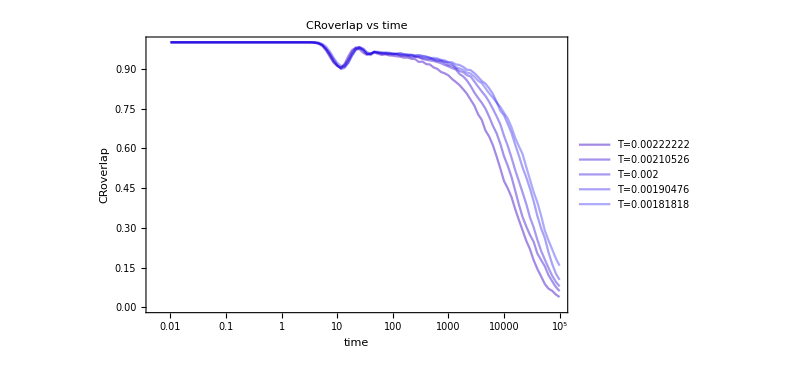

```mathematica
CRoverlapLongestPlot=ListLogLinearPlot[Table[Table[{timeLT[[rec]],CRoverlapMeanLongest[[T,rec]]},{rec,Length[CRoverlapMeanLongest[[T]]]}],{T,Length[TlistLongest]}],PlotLegends->Table["T="<>ToString[TlistLongest[[T]]],{T,Length[TlistLongest]}],PlotStyle->redBluePlotConfig[Length[Tlist]+Length[TlistLT]+Length[TlistLongest]][[Length[Tlist]+Length[TlistLT];;]],FrameLabel->{"time","CRoverlap"},ImageSize->600,PlotLabel->"CRoverlap vs time",Joined->True]
```

```mathematica
Table[{Normal[timeLongest[[rec]]],Normal[CRoverlapMeanLongest[[2,rec]]]},{rec,52,Length[timeLongest]}]
```

{{63.1,0.958822},{73.56,0.958171},{85.77,0.956543},{100.,0.955892},{116.59,0.955241},{135.94,0.952637},{158.49,0.951172},{184.78,0.947673},{215.44,0.951416},{251.19,0.945394},{292.86,0.943848},{341.45,0.937419},{398.11,0.934163},{464.16,0.931315},{541.17,0.929362},{630.96,0.925456},{735.64,0.921143},{857.7,0.914388},{1000.,0.909098},{1165.91,0.902832},{1359.36,0.897461},{1584.89,0.880452},{1847.85,0.871012},{2154.43,0.855957},{2511.89,0.835124},{2928.64,0.810547},{3414.55,0.790202},{3981.07,0.771729},{4641.59,0.749674},{5411.7,0.718994},{6309.57,0.685221},{7356.42,0.65682},{8576.96,0.617025},{10000.,0.57015},{11659.1,0.534505},{13593.6,0.493245},{15848.9,0.441488},{18478.5,0.388835},{21544.3,0.341471},{25118.9,0.30542},{29286.4,0.273275},{34145.5,0.247477},{39810.7,0.203125},{46415.9,0.178874},{54117.,0.155518},{63095.7,0.121582},{73564.2,0.0986328},{85769.6,0.0767415},{100000.,0.0612793}}

```mathematica
fitsCRoverlapLongest=Table[NonlinearModelFit[Table[{Normal[timeLongest[[rec]]],Normal[CRoverlapMeanLongest[[T,rec]]]},{rec,52,Length[timeLongest]}],{stretchedExp[t,G,τ,β],{1.0>β>0.2,1>G>0,τ>3}},{G,τ,β},t],{T,Length[TlistLongest]}];
```

```mathematica
fitsCRoverlapLongest["BestFitParameters"]
```

{FittedModel[0.973606 ⅇ^(-0.000578591 t^0.765277)],FittedModel[0.976955 ⅇ^(-0.000322894 t^0.801778)],FittedModel[0.965694 ⅇ^(-0.000137269 t^0.865234)],FittedModel[0.961696 ⅇ^(-0.000064361 t^0.912167)],FittedModel[0.962681 ⅇ^(-0.0001252 t^0.836894)]}[BestFitParameters]

```mathematica
tauCRoverlapfitsLongest=Table[fitsCRoverlapLongest[[T]]["BestFitParameters"][[2,2]],{T,Length[TlistLT]}]
```

{17008.4,22594.2,29109.1,39352.1,46020.2}

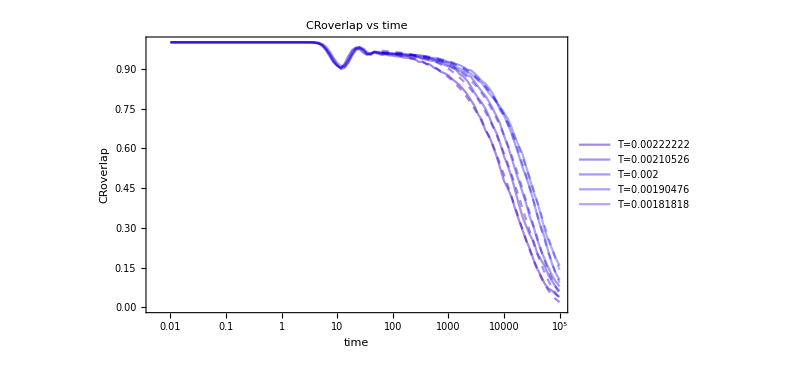

```mathematica
Show[CRoverlapLongestPlot,Table[LogLinearPlot[fitsCRoverlapLongest[[T]][x],{x,timeLT[[52]],100000},PlotRange->{{0.01,10000},{0,1}},PlotStyle->{Dashed,redBluePlotConfig[Length[Tlist]+Length[TlistLT]][[T+Length[Tlist]]]}],{T,Length[TlistLT]}]]
```

```mathematica
Export["/home/chengling/Research/updates/02012024/CRoverlap.jpeg",Show[CRoverlapfitST,CRoverlapLTPlot,Table[LogLinearPlot[fitsCRoverlapLT[[T]][x],{x,timeLT[[52]],100000},PlotRange->{{0.01,10000},{0,1}},PlotStyle->{Dashed,redBluePlotConfig[Length[Tlist]+Length[TlistLT]][[T+Length[Tlist]]]}],{T,Length[TlistLT]}]],ImageResolution->600];
```

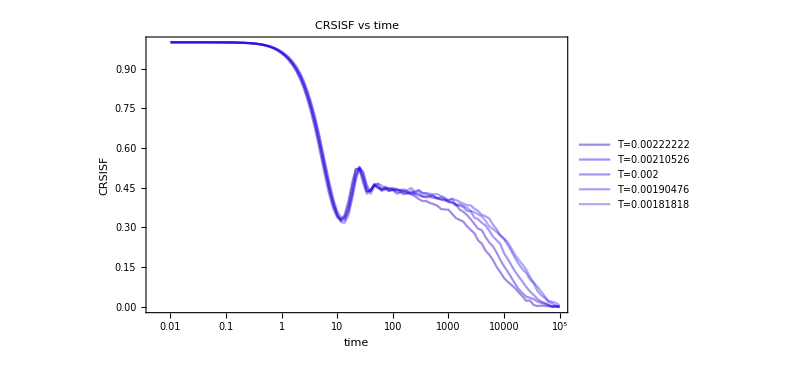

```mathematica
CRSISFLongestPlot=ListLogLinearPlot[Table[Table[{timeLT[[rec]],CRSISFMeanLongest[[T,rec]]},{rec,Length[CRoverlapMeanLongest[[T]]]}],{T,Length[TlistLongest]}],PlotLegends->Table["T="<>ToString[TlistLongest[[T]]],{T,Length[TlistLT]}],PlotStyle->redBluePlotConfig[Length[TlistAllT]][[Length[Tlist]+Length[TlistLT];;]],FrameLabel->{"time","CRSISF"},ImageSize->600,PlotLabel->"CRSISF vs time",Joined->True]
```

```mathematica
fitsCRSISFLongest=Table[NonlinearModelFit[Table[{Normal[timeLongest[[rec]]],Normal[CRSISFMeanLongest[[T,rec]]]},{rec,52,Length[timeLongest]}],{stretchedExp[t,G,τ,β],{0.81>β>0.2,0.5>G>0,τ>3}},{G,τ,β},t],{T,Length[TlistLongest]}];
```

```mathematica
fitsCRSISFLongest
```

{FittedModel[0.448606 ⅇ^(-0.000903807 t^(«19»))],FittedModel[0.457386 ⅇ^(-0.000607876 t^(«19»))],FittedModel[0.45083 ⅇ^(-0.000458899 t^(«19»))],FittedModel[0.452285 ⅇ^(-0.00034579 t^(«19»))],FittedModel[0.449566 ⅇ^(-0.000391055 t^(«19»))]}

```mathematica
tauCRSISFfitsLongest=Table[fitsCRSISFLongest[[T]]["BestFitParameters"][[2,2]],{T,Length[TlistLongest]}]
```

{6834.04,9346.07,13224.1,18754.3,19569.1}

```mathematica
Length[TlistLongest]
```

5

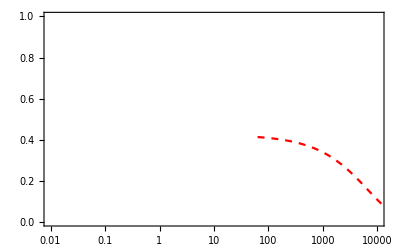
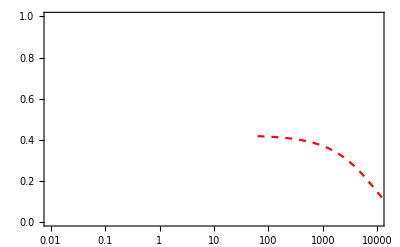
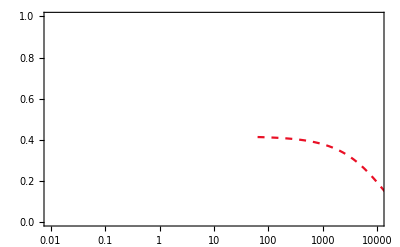
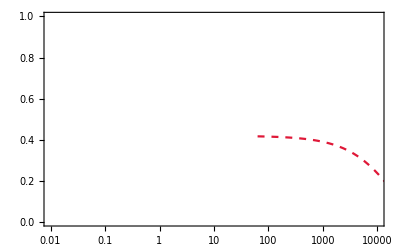
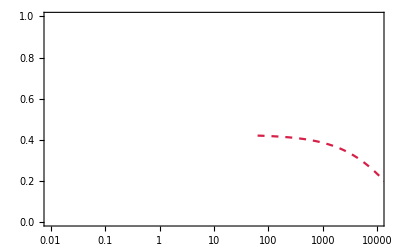

```mathematica
Table[LogLinearPlot[fitsCRSISFLongest[[T]][x],{x,timeLongest[[52]],100000},PlotRange->{{0.01,10000},{0,1}},PlotStyle->{Dashed,redBluePlotConfig[Length[TlistAllT]][[T]]}],{T,Length[TlistLongest]}]
```

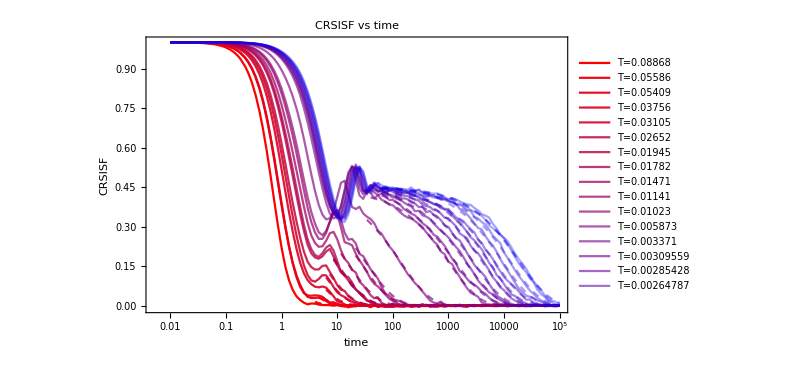

```mathematica
Show[CRSISFSTLTwithFitPlot,CRSISFLongestPlot,Table[LogLinearPlot[fitsCRSISFLongest[[T]][x],{x,timeLT[[52]],100000},PlotRange->{{0.01,10000},{0,1}},PlotStyle->{Dashed,redBluePlotConfig[Length[TlistAllT]][[T+Length[Tlist]+Length[TlistLT]]]}],{T,Length[TlistLongest]}]]
```

```mathematica
Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/CRSISF_p380.jpeg",Show[CRSISFSTLTwithFitPlot,CRSISFLongestPlot,Table[LogLinearPlot[fitsCRSISFLongest[[T]][x],{x,timeLT[[52]],100000},PlotRange->{{0.01,10000},{0,1}},PlotStyle->{Dashed,redBluePlotConfig[Length[TlistAllT]][[T+Length[Tlist]+Length[TlistLT]]]}],{T,Length[TlistLongest]}]]];
```

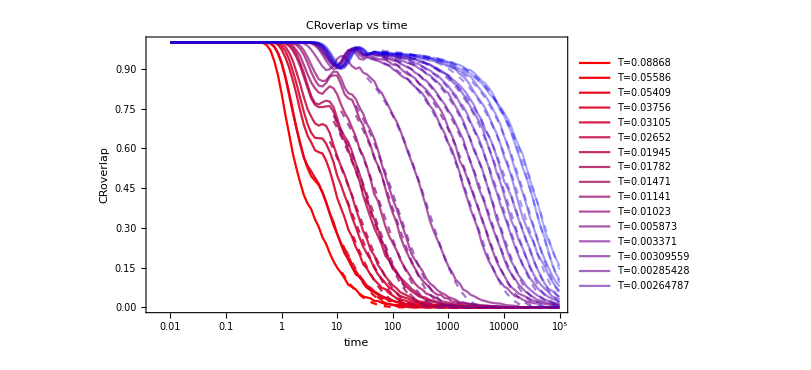

```mathematica
Show[CRoverlapSTLTwithFitPlot,CRoverlapLongestPlot,Table[LogLinearPlot[fitsCRoverlapLongest[[T]][x],{x,timeLT[[52]],100000},PlotRange->{{0.01,10000},{0,1}},PlotStyle->{Dashed,redBluePlotConfig[Length[TlistAllT]][[T+Length[Tlist]+Length[TlistLT]]]}],{T,Length[TlistLongest]}]]
```

```mathematica
Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/CRoverlap_p380.jpeg",Show[CRoverlapSTLTwithFitPlot,CRoverlapLongestPlot,Table[LogLinearPlot[fitsCRoverlapLongest[[T]][x],{x,timeLT[[52]],100000},PlotRange->{{0.01,10000},{0,1}},PlotStyle->{Dashed,redBluePlotConfig[Length[TlistAllT]][[T+Length[Tlist]+Length[TlistLT]]]}],{T,Length[TlistLongest]}]]];
```

```mathematica
tauCRoverlapAllT=Join[tauCRoverlapfits,tauCRoverlapfitsLT,tauCRoverlapfitsLongest]
```

{3.16039,6.7635,6.75448,12.5106,17.4891,23.0389,38.8819,42.9591,64.5399,101.84,125.531,436.846,2732.95,3582.02,5140.15,7160.55,10064.4,13246.9,17008.4,22594.2,29109.1,39352.1,46020.2}

```mathematica
tauCRSISFAllT=Join[tauCRSISFfits,tauCRSISFfitsLT,tauCRSISFfitsLongest]
```

{0.728537,1.41524,1.61389,2.6929,4.03698,5.21129,9.19522,9.51448,14.8936,25.9793,32.3344,138.256,1036.02,1239.22,2019.54,2804.8,4144.73,5262.53,6834.04,9346.07,13224.1,18754.3,19569.1}

```mathematica
TlistAllT=Join[Tlist,TlistLT,TlistLongest];
```

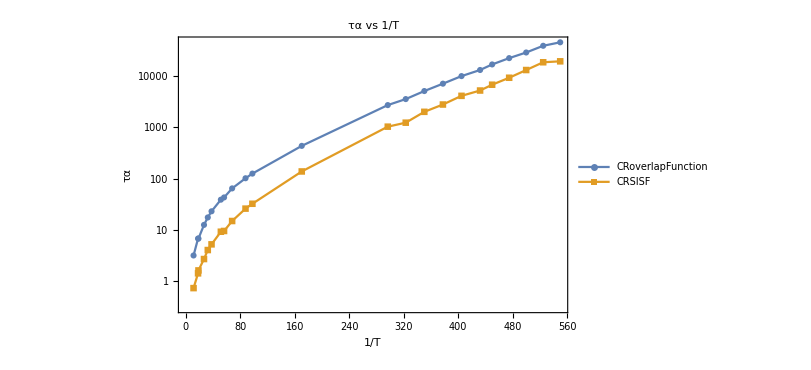

```mathematica
tauAlphafitingPlot=ListLogPlot[{Table[{1/TlistAllT[[T]],tauCRoverlapAllT[[T]]},{T,Length[TlistAllT]}],Table[{1/TlistAllT[[T]],tauCRSISFAllT[[T]]},{T,Length[TlistAllT]}]},FrameLabel->{"1/T","τα"},PlotLegends->{"CRoverlapFunction","CRSISF"},PlotMarkers->{Automatic},ImageSize->600,PlotLabel->"τα vs 1/T",Joined->True,PlotRange->All]
```

```mathematica
Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/tauAlpha_p380.jpeg",tauAlphafitingPlot];
```

```mathematica
Export["/home/chengling/Research/updates/02012024/taualpha.jpeg",tauAlphafitingPlot,ImageResolution->600];
```

```mathematica
betaCRSISFfitsAllT=Join[Table[fitsCRSISF[[T]]["BestFitParameters"][[3,2]],{T,Length[Tlist]}],Table[fitsCRSISFLT[[T]]["BestFitParameters"][[3,2]],{T,Length[TlistLT]}],Table[fitsCRSISFLongest[[T]]["BestFitParameters"][[3,2]],{T,Length[TlistLongest]}]]
```

{0.809979,0.796758,0.809037,0.809862,0.80979,0.809928,0.80995,0.809939,0.809968,0.80997,0.809986,0.809967,0.809928,0.703551,0.771414,0.809972,0.809195,0.809984,0.793789,0.809994,0.809994,0.809994,0.794059}

```mathematica
GCRSISFfitsAllT=Join[Table[fitsCRSISF[[T]]["BestFitParameters"][[1,2]],{T,Length[Tlist]}],Table[fitsCRSISFLT[[T]]["BestFitParameters"][[1,2]],{T,Length[TlistLT]}],Table[fitsCRSISFLongest[[T]]["BestFitParameters"][[1,2]],{T,Length[TlistLongest]}]]
```

{0.449978,0.437055,0.448006,0.449785,0.449754,0.449922,0.449957,0.449934,0.449975,0.449977,0.44999,0.449993,0.441588,0.473171,0.454078,0.449017,0.44834,0.455473,0.448606,0.457386,0.45083,0.452285,0.449566}

```mathematica
betaCRoverlapfitsAllT=Join[Table[fitsCRoverlap[[T]]["BestFitParameters"][[3,2]],{T,Length[Tlist]}],Table[fitsCRoverlapLT[[T]]["BestFitParameters"][[3,2]],{T,Length[TlistLT]}],Table[fitsCRoverlapLongest[[T]]["BestFitParameters"][[3,2]],{T,Length[TlistLongest]}]]
```

{0.529141,0.592079,0.569808,0.630995,0.641043,0.665991,0.691322,0.701875,0.704992,0.729689,0.738498,0.762204,0.759353,0.730815,0.74279,0.794476,0.764024,0.795187,0.765277,0.801778,0.865234,0.912167,0.836894}

```mathematica
GCRoverlapfitsAllT=Join[Table[fitsCRoverlap[[T]]["BestFitParameters"][[1,2]],{T,Length[Tlist]}],Table[fitsCRoverlapLT[[T]]["BestFitParameters"][[1,2]],{T,Length[TlistLT]}],Table[fitsCRoverlapLongest[[T]]["BestFitParameters"][[1,2]],{T,Length[TlistLongest]}]]
```

{0.999912,0.999974,0.999974,0.999988,0.999992,0.999993,0.999996,0.999996,0.999997,0.999996,0.999997,0.999998,0.980185,0.993608,0.988459,0.976593,0.980814,0.978599,0.973606,0.976955,0.965694,0.961696,0.962681}

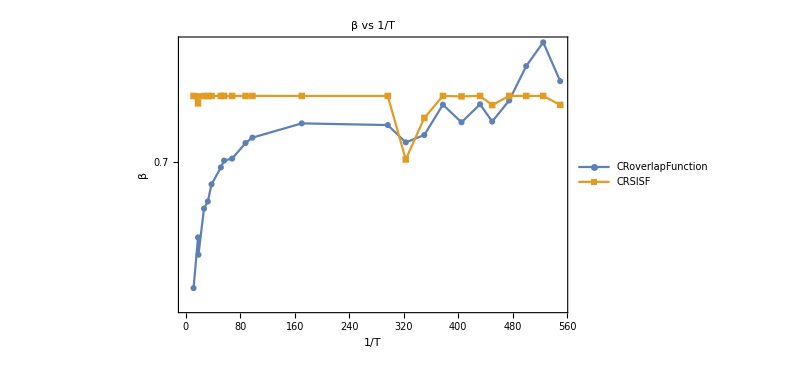

```mathematica
betafitingPlot=ListLogPlot[{Table[{1/TlistAllT[[T]],betaCRoverlapfitsAllT[[T]]},{T,Length[TlistAllT]}],Table[{1/TlistAllT[[T]],betaCRSISFfitsAllT[[T]]},{T,Length[TlistAllT]}]},FrameLabel->{"1/T","β"},PlotLegends->{"CRoverlapFunction","CRSISF"},PlotMarkers->{Automatic},ImageSize->600,PlotLabel->"β vs 1/T",Joined->True,PlotRange->All]
```

```mathematica
Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/fittingBeta_p380_p380.jpeg",betafitingPlot,ImageResolution->600];
```

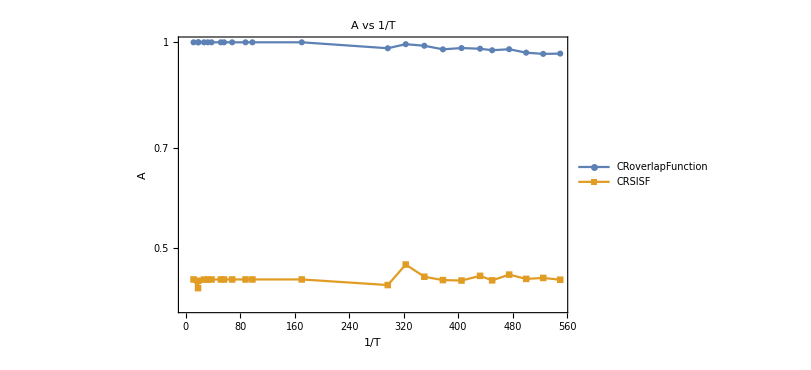

```mathematica
GfitingPlot=ListLogPlot[{Table[{1/TlistAllT[[T]],GCRoverlapfitsAllT[[T]]},{T,Length[TlistAllT]}],Table[{1/TlistAllT[[T]],GCRSISFfitsAllT[[T]]},{T,Length[TlistAllT]}]},FrameLabel->{"1/T","A"},PlotLegends->{"CRoverlapFunction","CRSISF"},PlotMarkers->{Automatic},ImageSize->600,PlotLabel->"A vs 1/T",Joined->True,PlotRange->All]
```

```mathematica
Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/fittingA_p380_p380.jpeg",GfitingPlot,ImageResolution->600];
```

```mathematica
tauCRoverlapAllT
```

{3.16039,6.7635,6.75448,12.5106,17.4891,23.0389,38.8819,42.9591,64.5399,101.84,125.531,436.846,2732.95,3582.02,5140.15,7160.55,10064.4,13246.9,17008.4,22594.2,29109.1,39352.1,46020.2}

```mathematica
tauTable=Prepend[Table[{TlistAllT[[T]],tauCRSISFAllT[[T]],tauCRoverlapAllT[[T]]},{T,Length[TlistAllT]}],{"T","τα CRSISF","τα CR overlap"}]
```

{{T,τα CRSISF,τα CR overlap},{0.08868,0.728537,3.16039},{0.05586,1.41524,6.7635},{0.05409,1.61389,6.75448},{0.03756,2.6929,12.5106},{0.03105,4.03698,17.4891},{0.02652,5.21129,23.0389},{0.01945,9.19522,38.8819},{0.01782,9.51448,42.9591},{0.01471,14.8936,64.5399},{0.01141,25.9793,101.84},{0.01023,32.3344,125.531},{0.005873,138.256,436.846},{0.003371,1036.02,2732.95},{0.00309559,1239.22,3582.02},{0.00285428,2019.54,5140.15},{0.00264787,2804.8,7160.55},{0.00246931,4144.73,10064.4},{0.0023133,5262.53,13246.9},{0.00222222,6834.04,17008.4},{0.00210526,9346.07,22594.2},{0.002,13224.1,29109.1},{0.00190476,18754.3,39352.1},{0.00181818,19569.1,46020.2}}

```mathematica
Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/tauAlphaTableP380.csv",tauTable,"CSV"]
```

/home/chengling/Research/Project/Cell/glassyDynamics/plots/tauAlphaTableP380.csv